## GME Lukin-Structure

NOTE: Some calculations are made using ParallelDo or ParallelTable, that use several cores of the CPU.

### Parameters

```mathematica
T0=AbsoluteTime[];
SetDirectory[NotebookDirectory[]];
(**************************************************)
(*parameters of the structure*)
a=1.0;(*lattice parameter*)
we=0.01;(*parameter used in the searching of the guided modes*)
rs=0.0833 ; (*radio of the outer holes *)
rl=0.15; (*radio of the inner holes*)
l=0.4; (* distance of the inner holes to the center of the unit cell*)
d=0.25 ; (*slab width*)
ex1=1; (*permittivity of the upper layer*)
ex3=1; (*permittivity of the lower layer*)
es=10.5625; (*permittivity of the slab backfground*)
er=1.0; (*permi+ttivity of the holes in the slab*)
S=Sqrt[3]/2*a^2; (*area of the unit cell*)
(*parameters of the calculation*)
gx=gy=9;(*Must be integer, give a idea of the basis size of the in-plane reciprocal lattice vector*)
Ng=3;(*Must be integer, number of guided modes for each g*)
sig=1;(*Must be integer*)
(**************************************************)
kx=2π/a* (1/Sqrt[3]); ky=2π/a* (1/3);(*Coordinates of the K point*)
(**************************************************)
```

```mathematica
Clear[coef,coef1, coef2,G,Cet,epsm,NTE,A2,B2,A3,NTM,C2,D2,C3,W1,W2,W3,X1,X2,X3,Y1,Y2,Y3,Z1,Z2,Z3];
```

```mathematica
Norm[{1/√3,1}]
```

2/(√3)

#### Basis of PW, circular cutoff

Here, the program select the set of G that will use to build up the basis of guided modes. It use a circular cutoff to chose the set, it is all the G vectos that satisfie the condition G ≤Gmax= gx* (4π)/(√3 a)

```mathematica
gg[n_,m_]:=2 π/a N[n*{1/√3,1}+m*{-1/√3,1}];gr[n_,m_,θ_]:=2π/a {{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}}.(n*{1/√3,1}+m*{-1/√3,1});Gmax=Norm[gg[gx,0]];
Gg={};
Do[ Do[If[Norm[gg[i,j]]≤Gmax,AppendTo[Gg,{i,j}]],{i,-2gx,2gx}],{j,-2gy,2gy}];
G[m_]:=G[m]=N[gg[Gg⟦m,1⟧,Gg⟦m,2⟧]];
lg=Length[Gg];
gmax=Max[Gg⟦All,1⟧];
Print["The set of G vectors have ", lg, " elements"]
```

The set of G vectors have 301 elements

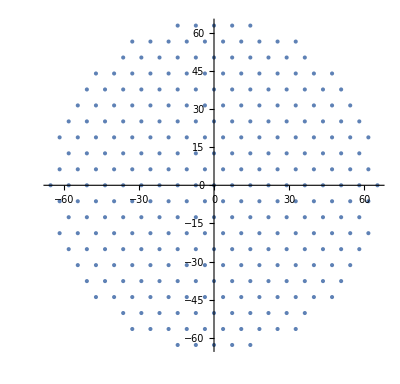

```mathematica
ListPlot[Table[G[m],{m,lg}],AspectRatio->Automatic] 
(*Each point in the plot represent a G vector we will use to build up the guided modes*)
```

### Permitivity Structure

Here, we define functions to describe the structure of the dielectric media. First, we define a piecewise function with the exact value of the permittivity at any r in the unit cell. Second, we  calculate the Fourier coefficients to expand the dielectric permittivity in the plane and construct the matrix elements η_(G-G')associated with the structure of the unit cell.

#### Analytic Dielectric Function

```mathematica
(*Mesh in the hexagonal unit cell to evaluated the permittivity, fields, Green functions or any other function of the position*)
Rlist=Flatten[Table[N[{xx,yy}],{xx,-Sqrt[3]/3,Sqrt[3]/3,(2/3Sqrt[3]/3)/50},{yy,-0.5,0.5,1/50}],1]; (*Mesh in a rectangular area*)
RHex={};(*Mesh in a hexagonal (unit cell) area*)
Do[{xX,yY}=Rlist⟦i⟧;
If[(Abs[xX]≤ Sqrt[3]/6 && Abs[yY] <=0.5),AppendTo[RHex,{xX,yY}],If[Abs[xX]≥  Sqrt[3]/6&& Abs[yY]≤  -Sqrt[3]Abs[xX]+1,AppendTo[RHex,{xX,yY}]]],{i,1,Length[Rlist]}];
(*Below, we define the analytical piecewise dielectric function in the unit cell*)
Eps[x_,y_]:=es-If[(Norm[Abs[{x,y}]-{Sqrt[3]/3,0}]≤ rs||Norm[Abs[{x,y}]-{Sqrt[3]/6,0.5}]≤ rs||Norm[Abs[{x,y}]-{0,0.5}]≤ rl||Norm[Abs[{x,y}]-{Sqrt[3]/4,0.25}]≤ rl),es-er,0]
```

```mathematica
EpsList=Table[{RHex⟦i,1⟧,RHex⟦i,2⟧,Eps[RHex⟦i,1⟧,RHex⟦i,2⟧]},{i,1,Length[RHex]}]; (*Evaluating the dielectric function in the unit cell mesh*)
```

```mathematica
(*We define the plot of the dielectric function, to be used before in some graphs*)
EpsGrap=ListDensityPlot[EpsList,ColorFunction->"GrayTones",PlotStyle-> Opacity[0.1]];
EpsGrapFull=ListDensityPlot[EpsList,ColorFunction->"GrayTones"];
```

#### Coefficients of dielectric structure

```mathematica
II[Gx_,Gy_]:=II[Gx,Gy]=NIntegrate[Integrate[Exp[ⅈ {Gx,Gy}.{xx,yy}],{xx,-√(rl^2-(0.5 a-l+yy)^2),0}],{yy,-(0.5 a-l+rl),0}]+NIntegrate[Integrate[Exp[ⅈ {Gx,Gy}.{xx,yy}],{xx,-√(rl^2-(0.5 a-l-yy)^2),0}],{yy,0,(0.5 a-l+rl)}]+NIntegrate[Integrate[Exp[ⅈ {Gx,Gy}.{xx,yy}],{xx,0,√(rl^2-(0.5 a-l+yy)^2)}],{yy,-(0.5 a-l+rl),0}]+NIntegrate[Integrate[Exp[ⅈ {Gx,Gy}.{xx,yy}],{xx,0,√(rl^2-(0.5 a-l-yy)^2)}],{yy,0,(0.5 a-l+rl)}];
coef1[n_,m_]:=coef1[n,m]=(er-es)/(√3 a^2/2)*If[Norm[gg[n,m]]==0, 2π rs^2,2 π rs BesselJ[1, rs Norm[gg[n,m]]]/Norm[gg[n,m]](Exp[ⅈ gg[n,m].{√3 a/3,0}]+Exp[ⅈ gg[n,m].{-√3 a/3,0}])];
coef2[n_,m_]:=coef2[n,m]=(er-es)/(√3 a^2/2)(Exp[ⅈ gg[n,m].{0,-0.5*a}]*II[gg[n,m][[1]],gg[n,m][[2]]]+Exp[ⅈ gg[n,m].{-√3 a/4,a/4}]II[gr[n,m,π/3][[1]],gr[n,m,π/3][[2]]]+Exp[ⅈ gg[n,m].{√3 a/4,a/4}]II[gr[n,m,-π/3][[1]],gr[n,m,-π/3][[2]]]);
coef[n_,m_]:=coef[n,m]=coef[-n,-m]=coef[m,n]=If[Norm[gg[n,m]]==0, es+coef1[n,m]+coef2[n,m],coef1[n,m]+coef2[n,m]];
```

```mathematica
Coef=Import["Coef-Eps-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat"];
```

#### Matrix for permitivity coeffients

```mathematica
Mets=Import["Matrix-Eta-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat","Table"];
Coefinv=Table[Mets⟦(Length[Mets]+1)/2,i⟧,{i,Length[Mets]}];
Cet[l_,m_,mp_]:=Cet[l,m,mp]=N[If[l==1,N[(1/ex1)]*IdentityMatrix[Length[Gg]]⟦m,mp⟧,If[l==2,Mets⟦m,mp⟧,If[l==3,N[(1/ex3)]*IdentityMatrix[Length[Gg]]⟦m,mp⟧]]]];
epsm[j_]:=epsm[j]=N[(2/(a a Sqrt[3])) If[j==1,ex1 a a Sqrt[3]/2,If[j==2,es*(a a Sqrt[3]/2-3*II[0,0]-2 π rs^2)+(3*II[0,0]+2 π rs^2)er,ex3 a a Sqrt[3]/2]]];
```

#### Plotting the expansion of permitivity

```mathematica
epsop[x_,y_]:=Chop[Sum[Coef⟦2*gmax+1+Gg⟦i,1⟧,2gmax +1+Gg⟦i,2⟧⟧ Exp[N[I G[i].{x,y}]],{i,Length[Gg]}]];
eps3D[x_,y_,z_]:=If[Abs[z]<=0.5d,epsop[x,y],1];
epsinvop[x_,y_]:=Chop[Sum[Coefinv⟦i⟧ Exp[N[I G[i].{x,y}]],{i,Length[Gg]}]];
```

```mathematica
listaepsop=ParallelTable[{x,y,epsop[x,y]},{x,-2Sqrt[3]/3,2Sqrt[3]/3,0.01},{y,-0.5,0.5,0.01}];
```

```mathematica
listaepsinvop=ParallelTable[{x,y,epsinvop[x,y]},{x,-2Sqrt[3]/3,2Sqrt[3]/3,0.01},{y,-0.5,0.5,0.01}];
```

```mathematica
ListDensityPlot[Flatten[listaepsinvop,1],AspectRatio->Automatic, PlotLegends-> Automatic]
(*ListDensityPlot[Flatten[listaEpsInvop,1],AspectRatio->Automatic, PlotLegends-> Automatic]*)
```

-Graphics-

```mathematica
Show[{ListDensityPlot[Flatten[listaepsop,1],ColorFunction->"TemperatureMap",FrameTicksStyle->Directive[Black,20],PlotRange->All,ColorFunction->"TemperatureMap",PlotLegends->Automatic,AspectRatio->Automatic],ListPlot[{{{-2Sqrt[3]/3,0},{2Sqrt[3]/3,0}},{{0,0}},{{0,-0.5},{0,0.5}}},Joined->True]}]
```

-Graphics-

### Init Structure

```mathematica
X[j_,g_,w_]:=N[Sqrt[g^2-epsm[j] (w^2)]];
qg[g_,w_]:=N[Sqrt[epsm[2] (w^2)-g^2]];
TEsigp[g_,w_]:=N[qg[g,w] Sin[qg[g,w] 0.5 d]-X[1,g,w] Cos[qg[g,w] 0.5 d]];
TEsigm[g_,w_]:=N[qg[g,w] Cos[qg[g,w] 0.5 d]+X[1,g,w] Sin[qg[g,w] 0.5 d]];
TMsigp[g_,w_]:=N[(qg[g,w]/epsm[2]) Cos[qg[g,w] 0.5 d]+(X[1,g,w]/epsm[1]) Sin[qg[g,w] 0.5 d]];
TMsigm[g_,w_]:=N[(qg[g,w]/epsm[2]) Sin[qg[g,w] 0.5 d]-(X[1,g,w]/epsm[1]) Cos[qg[g,w] 0.5 d]];
If[sig==1,If[Mod[Ng,2]==0,Ngte=Ngtm=Ng/2,Ngte=0.5 (Ng+1);
Ngtm=0.5 (Ng-1)],If[Mod[Ng,2]==0,Ngte=Ngtm=Ng/2,Ngte=0.5 (Ng-1);
Ngtm=0.5 (Ng+1)]];
eg[g_]:=Normalize[{-g[[2]],g[[1]]}];
A2p[g_,w_]:=N[0.5 (qg[g,w]-I X[1,g,w]) Exp[I qg[g,w] 0.5 d]/qg[g,w]];
B2p[g_,w_]:=N[0.5 (qg[g,w]+I X[1,g,w]) Exp[-I qg[g,w] 0.5 d]/qg[g,w]];
A3p[g_,w_]:=N[0.5 (qg[g,w] (X[3,g,w]-X[1,g,w]) Cos[qg[g,w] d]+(qg[g,w]^2+X[1,g,w] X[3,g,w]) Sin[qg[g,w] d])/(qg[g,w] X[3,g,w])];
NTE[g_,w_]:=NTE[g,w]=Chop[Sqrt[1/(((X[1,g,w]^2+g^2)/(2 X[1,g,w]))+(((X[3,g,w]^2+g^2) (Norm[A3p[g,w]]^2))/(2 X[3,g,w]))+d ((g^2+qg[g,w]^2) (Norm[A2p[g,w]]^2+Norm[B2p[g,w]]^2)+((g^2-qg[g,w]^2) (Conjugate[A2p[g,w]] B2p[g,w]+Conjugate[B2p[g,w]] A2p[g,w]) Sin[qg[g,w] d]/(qg[g,w] d))))]];
A2[g_,w_]:=A2[g,w]=NTE[g,w] A2p[g,w];
B2[g_,w_]:=B2[g,w]=NTE[g,w] B2p[g,w];
A3[g_,w_]:=A3[g,w]=NTE[g,w] A3p[g,w];
C2p[g_,w_]:=((qg[g,w]/epsm[2])-I (X[1,g,w]/epsm[1])) Exp[I qg[g,w] d/2]/(2 (qg[g,w]/epsm[2]));
D2p[g_,w_]:=((qg[g,w]/epsm[2])+I (X[1,g,w]/epsm[1])) Exp[-I qg[g,w] d/2]/(2 (qg[g,w]/epsm[2]));
C3p[g_,w_]:=((qg[g,w]/epsm[2]) ((X[3,g,w]/epsm[3])-(X[1,g,w]/epsm[1])) Cos[qg[g,w] d]+((qg[g,w]/epsm[2])^2+(X[1,g,w]/epsm[1]) (X[3,g,w]/epsm[3])) Sin[qg[g,w] d])/(2 (qg[g,w]/epsm[2]) (X[3,g,w]/epsm[3]));
NTM[g_,w_]:=NTM[g,w]=Chop[Sqrt[1/((1/(2 X[1,g,w]))+((Norm[C3p[g,w]]^2)/(2 X[3,g,w]))+d (Norm[C2p[g,w]]^2+Norm[D2p[g,w]]^2+(Conjugate[C2p[g,w]] D2p[g,w]+Conjugate[D2p[g,w]] C2p[g,w]) Sin[qg[g,w] d]/(qg[g,w] d)))]];
C2[g_,w_]:=C2[g,w]=NTM[g,w] C2p[g,w];
D2[g_,w_]:=D2[g,w]=NTM[g,w] D2p[g,w];
C3[g_,w_]:=C3[g,w]=NTM[g,w] C3p[g,w];
I1[g_,gp_,w_,wp_]:=(X[1,g,w]+X[1,gp,wp])^(-1);
I2p[g_,gp_,w_,wp_]:=Sin[(qg[g,w]+qg[gp,wp]) d/2]/((qg[g,w]+qg[gp,wp])/2);
I2m[g_,gp_,w_,wp_]:=If[(qg[g,w]-qg[gp,wp])==0,d,Sin[(qg[g,w]-qg[gp,wp]) d/2]/((qg[g,w]-qg[gp,wp])/2)];
I3[g_,gp_,w_,wp_]:=(X[3,g,w]+X[3,gp,wp])^(-1);
q[j_,g_,w_]:=N[Sqrt[epsm[j] (w^2)-g^2]];
Mte21[g_,w_]:=N[(1/(2 q[2,g,w]))*{{(q[2,g,w]+q[1,g,w]) Exp[0.5I q[2,g,w] d],(q[2,g,w]-q[1,g,w]) Exp[0.5I q[2,g,w] d]},{(q[2,g,w]-q[1,g,w]) Exp[-0.5I q[2,g,w] d],(q[2,g,w]+q[1,g,w]) Exp[-0.5I q[2,g,w] d]}}];
Mte32[g_,w_]:=N[(0.5/ q[3,g,w])*{{(q[3,g,w]+q[2,g,w]) Exp[0.5I q[2,g,w] d],(q[3,g,w]-q[2,g,w]) Exp[-0.5I q[2,g,w] d]},{(q[3,g,w]-q[2,g,w]) Exp[0.5I q[2,g,w] d],(q[3,g,w]+q[2,g,w]) Exp[-0.5I q[2,g,w] d]}}];
Mte31[g_,w_]:=N[(0.25/(q[2,g,w]q[3,g,w])){{(q[2,g,w]+q[1,g,w])(q[3,g,w]+q[2,g,w])Exp[I q[2,g,w] d]+(q[2,g,w]-q[1,g,w])(q[3,g,w]-q[2,g,w])Exp[-I q[2,g,w] d],(q[2,g,w]-q[1,g,w])(q[3,g,w]+q[2,g,w])Exp[I q[2,g,w] d]+(q[2,g,w]+q[1,g,w])(q[3,g,w]-q[2,g,w])Exp[-I q[2,g,w] d]},{(q[2,g,w]+q[1,g,w])(q[3,g,w]-q[2,g,w])Exp[I q[2,g,w] d]+(q[2,g,w]-q[1,g,w])(q[3,g,w]+q[2,g,w])Exp[-I q[2,g,w] d],(q[2,g,w]-q[1,g,w])(q[3,g,w]-q[2,g,w])Exp[I q[2,g,w] d]+(q[2,g,w]+q[1,g,w])(q[3,g,w]+q[2,g,w])Exp[-I q[2,g,w] d]}}];
X1l=N[1/Sqrt[epsm[1]]];
W1l[g_,w_]:=-(Mte31[g,w][[1,2]]/Mte31[g,w][[1,1]]) X1l;
W2l[g_,w_]:=Mte21[g,w][[1,1]] W1l[g,w]+Mte21[g,w][[1,2]] X1l;
X2l[g_,w_]:=Mte21[g,w][[2,1]] W1l[g,w]+Mte21[g,w][[2,2]] X1l;
W3l=N[0];
X3l[g_,w_]:=Mte32[g,w][[2,1]] W2l[g,w]+Mte32[g,w][[2,2]] X2l[g,w];
W3u=N[1/Sqrt[epsm[3]]];
X3u[g_,w_]:=(Mte31[g,w][[2,1]]/Mte31[g,w][[1,1]]) W3u;
W1u[g_,w_]:=W3u/Mte31[g,w][[1,1]];
X1u=N[0];
W2u[g_,w_]:=Mte21[g,w][[1,1]] W1u[g,w];
X2u[g_,w_]:=Mte21[g,w][[2,1]] W1u[g,w];
W1[g_,w_,j_]:=W1[g,w,j]=If[j==1,W1l[g,w],If[j==3,W1u[g,w]]];
W2[g_,w_,j_]:=W2[g,w,j]=If[j==1,W2l[g,w],If[j==3,W2u[g,w]]];
W3[g_,w_,j_]:=W3[g,w,j]=If[j==1,W3l,If[j==3,W3u]];
X1[g_,w_,j_]:=X1[g,w,j]=If[j==1,X1l,If[j==3,X1u]];
X2[g_,w_,j_]:=X2[g,w,j]=If[j==1,X2l[g,w],If[j==3,X2u[g,w]]];
X3[g_,w_,j_]:=X3[g,w,j]=If[j==1,X3l[g,w],If[j==3,X3u[g,w]]];
Mtm21[g_,w_]:=N[(0.5/(q[2,g,w]/epsm[2]))*{{((q[2,g,w]/epsm[2])+(q[1,g,w]/epsm[1])) Exp[0.5I q[2,g,w] d],((q[2,g,w]/epsm[2])-(q[1,g,w]/epsm[1])) Exp[0.5I q[2,g,w] d]},{((q[2,g,w]/epsm[2])-(q[1,g,w]/epsm[1])) Exp[-0.5I q[2,g,w] d],((q[2,g,w]/epsm[2])+(q[1,g,w]/epsm[1])) Exp[-0.5I q[2,g,w] d]}}];
Mtm32[g_,w_]:=N[(0.5/(q[3,g,w]/epsm[3]))*{{((q[3,g,w]/epsm[3])+(q[2,g,w]/epsm[2])) Exp[0.5I q[2,g,w] d],((q[3,g,w]/epsm[3])-(q[2,g,w]/epsm[2])) Exp[-0.5I q[2,g,w] d]},{((q[3,g,w]/epsm[3])-(q[2,g,w]/epsm[2])) Exp[0.5I q[2,g,w] d],((q[3,g,w]/epsm[3])+(q[2,g,w]/epsm[2])) Exp[-0.5I q[2,g,w] d]}}];
Mtm31[g_,w_]:=N[(0.25/(q[2,g,w]q[3,g,w]/(epsm[2]epsm[3]))){{(q[2,g,w]/epsm[2]+q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]+q[2,g,w]/epsm[2])Exp[I q[2,g,w] d]+(q[2,g,w]/epsm[2]-q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]-q[2,g,w]/epsm[2])Exp[-I q[2,g,w] d],(q[2,g,w]/epsm[2]-q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]+q[2,g,w]/epsm[2])Exp[I q[2,g,w] d]+(q[2,g,w]/epsm[2]+q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]-q[2,g,w]/epsm[2])Exp[-I q[2,g,w] d]},{(q[2,g,w]/epsm[2]+q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]-q[2,g,w]/epsm[2])Exp[I q[2,g,w] d]+(q[2,g,w]/epsm[2]-q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]+q[2,g,w]/epsm[2])Exp[-I q[2,g,w] d],(q[2,g,w]/epsm[2]-q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]-q[2,g,w]/epsm[2])Exp[I q[2,g,w] d]+(q[2,g,w]/epsm[2]+q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]+q[2,g,w]/epsm[2])Exp[-I q[2,g,w] d]}}];
Z1l=N[1];
Y1l[g_,w_]:=-(Mtm31[g,w][[1,2]]/Mtm31[g,w][[1,1]]) Z1l;
Y2l[g_,w_]:=Mtm21[g,w][[1,1]] Y1l[g,w]+Mtm21[g,w][[1,2]] Z1l;
Z2l[g_,w_]:=Mtm21[g,w][[2,1]] Y1l[g,w]+Mtm21[g,w][[2,2]] Z1l;
Y3l=N[0];
Z3l[g_,w_]:=Mtm32[g,w][[2,1]] Y2l[g,w]+Mtm32[g,w][[2,2]] Z2l[g,w];
Y3u=N[1];
Z3u[g_,w_]:=(Mtm31[g,w][[2,1]]/Mtm31[g,w][[1,1]]) Y3u;
Y1u[g_,w_]:=Y3u/Mtm31[g,w][[1,1]];
Z1u=N[0];
Y2u[g_,w_]:=Mtm21[g,w][[1,1]] Y1u[g,w];
Z2u[g_,w_]:=Mtm21[g,w][[2,1]] Y1u[g,w];
Y1[g_,w_,j_]:=Y1[g,w,j]=If[j==1,Y1l[g,w],If[j==3,Y1u[g,w]]];
Y2[g_,w_,j_]:=Y2[g,w,j]=If[j==1,Y2l[g,w],If[j==3,Y2u[g,w]]];
Y3[g_,w_,j_]:=Y3[g,w,j]=If[j==1,Y3l,If[j==3,Y3u]];
Z1[g_,w_,j_]:=Z1[g,w,j]=If[j==1,Z1l,If[j==3,Z1u]];
Z2[g_,w_,j_]:=Z2[g,w,j]=If[j==1,Z2l[g,w],If[j==3,Z2u[g,w]]];
Z3[g_,w_,j_]:=Z3[g,w,j]=If[j==1,Z3l[g,w],If[j==3,Z3u[g,w]]];
Ir1p[g_,gp_,w_,wp_]:=(X[1,g,w]+I q[1,gp,wp])^(-1);
Ir1m[g_,gp_,w_,wp_]:=(X[1,g,w]-I q[1,gp,wp])^(-1);
Ir2p[g_,gp_,w_,wp_]:=Sin[0.5(qg[g,w]+q[2,gp,wp]) d]/(0.5(qg[g,w]+q[2,gp,wp]));
Ir2m[g_,gp_,w_,wp_]:=If[(qg[g,w]-q[2,gp,wp])==0,d,Sin[0.5(qg[g,w]-q[2,gp,wp]) d]/(0.5(qg[g,w]-q[2,gp,wp]))];
Ir3p[g_,gp_,w_,wp_]:=(X[3,g,w]+I q[3,gp,wp])^(-1);
Ir3m[g_,gp_,w_,wp_]:=(X[3,g,w]-I q[3,gp,wp])^(-1);
```

### Bands

Here, we define the routines to calculate the band structures and modes of the photonic crystal slab. There are three routines, the first one is the sames as in the 1-GME.nb; the second, we have a routine that use saved GME-matrix elements for calculate the eigenproblem at K or K’; and finally, the third (fourth) routine use the saved GME-matrix elements to solve the eigenproblem at point k_1(k_1’) close to the Dirac cone at K(K’).

NOTE: The eigenvalues, eigenvectors and spatial modes of the fields are sort by frequency from the biggest one to the lowest. So, the index 1 is associated with the biggest eigenvalue and the largest index is associated with the lowest eigenvalue.

#### Bands Modules

WV Completa

```mathematica
WV[k0_,nb_,wv_]:=Module[{k=k0},
solTE={};solTM={};gs=Table[k+G[m],{m,lg}];
Do[g=Norm[gs⟦i⟧];
wmin=N[g/Sqrt[epsm[2]]+(10^-10)];wmax=N[g/Max[{Sqrt[epsm[1]],Sqrt[epsm[3]]}]-(10^-10)];dw=(wmax-wmin)/If[Round[(wmax-wmin)/we]<2,2,Round[(wmax-wmin)/we]];semte={}; semtm={};If[Ngte!=0,Do[If[Sign[If[sig==1,TEsigp[g,w],TEsigm[g,w]]]!=0&&Sign[If[sig==1,TEsigp[g,w],TEsigm[g,w]]]!=Sign[If[sig==1,TEsigp[g,w+dw],TEsigm[g,w+dw]]],AppendTo[semte,w];If[Length[semte]>=Ngte,Break[]]],{w,wmin,wmax-dw,dw}]];If[Ngtm!=0,Do[If[Sign[If[sig==1,TMsigp[g,w],TMsigm[g,w]]]!=0&&Sign[If[sig==1,TMsigp[g,w],TMsigm[g,w]]]!=Sign[If[sig==1,TMsigp[g,w+dw],TMsigm[g,w+dw]]],AppendTo[semtm,w];If[Length[semtm]>=Ngtm,Break[]]],{w,wmin,wmax-dw,dw}]];If[semte!={},sol1TE=wf/.FindRoot[If[sig==1,TEsigp[g,wf],TEsigm[g,wf]]==0,{wf,semte}];Do[AppendTo[solTE,{i,Chop[sol1TE]⟦j⟧}],{j,Length[Chop[sol1TE]]}]];If[semtm!={},sol1TM=wf/.FindRoot[If[sig==1,TMsigp[g,wf],TMsigm[g,wf]]==0,{wf,semtm}];Do[AppendTo[solTM,{i,Chop[sol1TM]⟦j⟧}],{j,Length[Chop[sol1TM]]}]],{i,lg}];Htete[mu_,nu_]:=N[Chop[(solTE⟦mu,2⟧^2) (solTE⟦nu,2⟧^2) (eg[gs⟦solTE⟦mu,1⟧⟧].eg[gs⟦solTE⟦nu,1⟧⟧]) ((epsm[1]^2) Cet[1,solTE⟦mu,1⟧,solTE⟦nu,1⟧] Conjugate[NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] NTE[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧] I1[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTE⟦nu,2⟧]+(epsm[3]^2) Cet[3,solTE⟦mu,1⟧,solTE⟦nu,1⟧] Conjugate[A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] A3[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧] I3[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTE⟦nu,2⟧]+(epsm[2]^2) Cet[2,solTE⟦mu,1⟧,solTE⟦nu,1⟧] ((Conjugate[A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] A2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]+Conjugate[B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] B2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]) I2m[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTE⟦nu,2⟧]+(Conjugate[A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] B2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]+Conjugate[B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] A2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]) I2p[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTE⟦nu,2⟧]))]];Htmtm[mu_,nu_]:=N[Chop[Cet[1,solTM⟦mu,1⟧,solTM⟦nu,1⟧] Conjugate[NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] NTM[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] (X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[1,Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] (Normalize[gs⟦solTM⟦mu,1⟧⟧].Normalize[gs⟦solTM⟦nu,1⟧⟧])+Norm[gs⟦solTM⟦mu,1⟧⟧] Norm[gs⟦solTM⟦nu,1⟧⟧]) I1[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTM⟦nu,2⟧]+Cet[3,solTM⟦mu,1⟧,solTM⟦nu,1⟧] Conjugate[C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] C3[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] (X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[3,Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] (Normalize[gs⟦solTM⟦mu,1⟧⟧].Normalize[gs⟦solTM⟦nu,1⟧⟧])+Norm[gs⟦solTM⟦mu,1⟧⟧] Norm[gs⟦solTM⟦nu,1⟧⟧]) I3[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTM⟦nu,2⟧]+Cet[2,solTM⟦mu,1⟧,solTM⟦nu,1⟧] ((Conjugate[C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] C2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]+Conjugate[D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] D2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]) (qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] qg[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] (Normalize[gs⟦solTM⟦mu,1⟧⟧].Normalize[gs⟦solTM⟦nu,1⟧⟧])+Norm[gs⟦solTM⟦mu,1⟧⟧] Norm[gs⟦solTM⟦nu,1⟧⟧]) I2m[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTM⟦nu,2⟧]+(Conjugate[C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] D2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]+Conjugate[D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] C2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]) (-qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] qg[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] (Normalize[gs⟦solTM⟦mu,1⟧⟧].Normalize[gs⟦solTM⟦nu,1⟧⟧])+Norm[gs⟦solTM⟦mu,1⟧⟧] Norm[gs⟦solTM⟦nu,1⟧⟧]) I2p[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTM⟦nu,2⟧])]];Htetm[mu_,nu_]:=N[Chop[(solTE⟦mu,2⟧^2) (eg[gs⟦solTE⟦mu,1⟧⟧].Normalize[gs⟦solTM⟦nu,1⟧⟧]) (-epsm[1] Cet[1,solTE⟦mu,1⟧,solTM⟦nu,1⟧] Conjugate[NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] NTM[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] X[1,Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] I1[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTM⟦nu,2⟧]+epsm[3] Cet[3,solTE⟦mu,1⟧,solTM⟦nu,1⟧] Conjugate[A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] C3[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] X[3,Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] I3[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTM⟦nu,2⟧]+I epsm[2] Cet[2,solTE⟦mu,1⟧,solTM⟦nu,1⟧] qg[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] ((-Conjugate[A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] C2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]+Conjugate[B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] D2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]) I2m[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTM⟦nu,2⟧]+(Conjugate[A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] D2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]-Conjugate[B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] C2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]) I2p[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTM⟦nu,2⟧]))]];Htmte[mu_,nu_]:=N[Chop[(solTE⟦nu,2⟧^2) (Normalize[gs⟦solTM⟦mu,1⟧⟧].eg[gs⟦solTE⟦nu,1⟧⟧]) (-epsm[1] Cet[1,solTM⟦mu,1⟧,solTE⟦nu,1⟧] Conjugate[NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] NTE[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧] X[1,Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧] I1[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTE⟦nu,2⟧]+epsm[3] Cet[3,solTM⟦mu,1⟧,solTE⟦nu,1⟧] Conjugate[C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] A3[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧] X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I3[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTE⟦nu,2⟧]-I epsm[2] Cet[2,solTM⟦mu,1⟧,solTE⟦nu,1⟧] qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] ((-Conjugate[C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] A2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]+Conjugate[D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] B2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]) I2m[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTE⟦nu,2⟧]+(Conjugate[D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] A2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]-Conjugate[C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] B2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]) I2p[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTE⟦nu,2⟧]))]];
NeTe=Length[solTE];
NeTm=Length[solTM];
Do[MH[m,n]=Htmtm[m,n],{m,NeTm},{n,NeTm}];Do[MH[m+NeTm,n+NeTm]=Htete[m,n],{m,NeTe},{n,NeTe}];Do[MH[m,n+NeTm]=Htmte[m,n],{m,NeTm},{n,NeTe}];Do[MH[m+NeTm,n]=Htetm[m,n],{m,NeTe},{n,NeTm}];MM=Table[MH[i,j],{i,NeTe+NeTm},{j,NeTe+NeTm}];If[HermitianMatrixQ[Chop[SetPrecision[MM,10]]]==False,Print["Non-Hermitian Matrix"];Abort[]];Eigenproblem=Eigensystem[Chop[MM],-nb];frecs=a*Sqrt[N[Eigenproblem⟦1⟧]]/(2 Pi);CoefMM=N[Eigenproblem⟦2⟧];Dxx={};Dyy={};Dzz={};
Hxx={};
Hyy={};
Hzz={};
Do[vkf=CoefMM⟦in⟧;HgTEx[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],-NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTE⟦mu,1⟧⟧]⟦1⟧;HgTEy[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],-NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTE⟦mu,1⟧⟧]⟦2⟧;HgTEz[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]];DgTEx[x_,y_,z_,mu_]:=I Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}] solTE⟦mu,2⟧ If[z>0.5d,epsm[3]A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,epsm[2]A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+epsm[2]B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],epsm[1]NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE[[mu,2]]] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTE⟦mu,1⟧⟧]⟦1⟧;DgTEy[x_,y_,z_,mu_]:=I Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}] solTE⟦mu,2⟧ If[z>0.5d,epsm[3]A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,epsm[2]A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+epsm[2]B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],epsm[1]NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTE⟦mu,1⟧⟧]⟦2⟧;HgTMx[x_,y_,z_,mu_]:=Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}] If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;HgTMy[x_,y_,z_,mu_]:=Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}] If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;DgTMx[x_,y_,z_,mu_]:=(I Exp[I N[gs⟦solTM⟦mu,1⟧⟧].{x,y}]/N[solTM⟦mu,2⟧])If[z>0.5d,C3[Norm[N[gs⟦solTM⟦mu,1⟧⟧]],N[solTM⟦mu,2⟧]] X[3,Norm[N[gs⟦solTM⟦mu,1⟧⟧]],solTM⟦mu,2⟧] Exp[-X[3,Norm[N[gs⟦solTM⟦mu,1⟧⟧]],N[solTM⟦mu,2⟧]] (z-0.5d)],If[Abs[z]<=0.5d,-C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],-NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;DgTMy[x_,y_,z_,mu_]:=(I Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}]/solTM⟦mu,2⟧)If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],-NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTM⟦mu,1⟧⟧]⟦2⟧;DgTMz[x_,y_,z_,mu_]:=(I Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}]/solTM⟦mu,2⟧)*If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]];

Hx[x_,y_,z_]:=N[Sum[vkf⟦mu⟧HgTMx[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧HgTEx[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Hy[x_,y_,z_]:=N[Sum[vkf⟦mu⟧HgTMy[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧HgTEy[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Hz[x_,y_,z_]:=N[Sum[vkf⟦mu+NeTm⟧HgTEz[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Dx[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMx[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧solTE⟦mu,2⟧DgTEx[x,y,z,mu],{mu,NeTe}]]/(2 Pi frecs⟦in⟧/Sqrt[S]);Dy[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMy[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧solTE⟦mu,2⟧DgTEy[x,y,z,mu],{mu,NeTe}]]/(2 Pi frecs⟦in⟧/Sqrt[S]);Dz[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMz[x,y,z,mu],{mu,NeTm}]]/(2 Pi frecs⟦in⟧/a*Sqrt[S]);AppendTo[Hxx,Hx[x,y,z]];AppendTo[Hyy,Hy[x,y,z]];AppendTo[Hzz,Hz[x,y,z]];AppendTo[Dxx,Dx[x,y,z]];AppendTo[Dyy,Dy[x,y,z]];AppendTo[Dzz,Dz[x,y,z]];
,{in,nb}];
{k,frecs,CoefMM,Hxx,Hyy,Hzz,Dxx,Dyy,Dzz}
];
```

WV reading a symmetric point k

```mathematica
WVrec[k0_,nb_,wv_]:=Module[{k=k0},
solTE={};solTM={};gs=Table[k+G[m],{m,lg}];
Do[g=Norm[gs⟦i⟧];
wmin=N[g/Sqrt[epsm[2]]+(10^-10)];wmax=N[g/Max[{Sqrt[epsm[1]],Sqrt[epsm[3]]}]-(10^-10)];dw=(wmax-wmin)/If[Round[(wmax-wmin)/we]<2,2,Round[(wmax-wmin)/we]];semte={}; semtm={};If[Ngte!=0,Do[If[Sign[If[sig==1,TEsigp[g,w],TEsigm[g,w]]]!=0&&Sign[If[sig==1,TEsigp[g,w],TEsigm[g,w]]]!=Sign[If[sig==1,TEsigp[g,w+dw],TEsigm[g,w+dw]]],AppendTo[semte,w];If[Length[semte]>=Ngte,Break[]]],{w,wmin,wmax-dw,dw}]];If[Ngtm!=0,Do[If[Sign[If[sig==1,TMsigp[g,w],TMsigm[g,w]]]!=0&&Sign[If[sig==1,TMsigp[g,w],TMsigm[g,w]]]!=Sign[If[sig==1,TMsigp[g,w+dw],TMsigm[g,w+dw]]],AppendTo[semtm,w];If[Length[semtm]>=Ngtm,Break[]]],{w,wmin,wmax-dw,dw}]];If[semte!={},sol1TE=wf/.FindRoot[If[sig==1,TEsigp[g,wf],TEsigm[g,wf]]==0,{wf,semte}];Do[AppendTo[solTE,{i,Chop[sol1TE]⟦j⟧}],{j,Length[Chop[sol1TE]]}]];If[semtm!={},sol1TM=wf/.FindRoot[If[sig==1,TMsigp[g,wf],TMsigm[g,wf]]==0,{wf,semtm}];Do[AppendTo[solTM,{i,Chop[sol1TM]⟦j⟧}],{j,Length[Chop[sol1TM]]}]],{i,lg}];
NeTe=Length[solTE];
NeTm=Length[solTM];
MM=Import["MatrixGME-kx_"<>ToString[k0⟦1⟧]<>"-ky_"<>ToString[k0⟦2⟧]<>"-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat","Table"];If[HermitianMatrixQ[Chop[SetPrecision[MM,10]]]==False,Print["Non-Hermitian Matrix"];Abort[]];Eigenproblem=Eigensystem[Chop[MM],-nb];frecs=a*Sqrt[N[Eigenproblem⟦1⟧]]/(2 Pi);CoefMM=N[Eigenproblem⟦2⟧];Dxx={};Dyy={};Dzz={};
Hxx={};
Hyy={};
Hzz={};
Do[vkf=CoefMM⟦in⟧;HgTEx[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],-NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTE⟦mu,1⟧⟧]⟦1⟧;HgTEy[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],-NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTE⟦mu,1⟧⟧]⟦2⟧;HgTEz[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]];DgTEx[x_,y_,z_,mu_]:=I Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}] solTE⟦mu,2⟧ If[z>0.5d,epsm[3]A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,epsm[2]A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+epsm[2]B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],epsm[1]NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE[[mu,2]]] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTE⟦mu,1⟧⟧]⟦1⟧;DgTEy[x_,y_,z_,mu_]:=I Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}] solTE⟦mu,2⟧ If[z>0.5d,epsm[3]A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,epsm[2]A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+epsm[2]B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],epsm[1]NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTE⟦mu,1⟧⟧]⟦2⟧;HgTMx[x_,y_,z_,mu_]:=Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}] If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;HgTMy[x_,y_,z_,mu_]:=Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}] If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;DgTMx[x_,y_,z_,mu_]:=(I Exp[I N[gs⟦solTM⟦mu,1⟧⟧].{x,y}]/N[solTM⟦mu,2⟧])If[z>0.5d,C3[Norm[N[gs⟦solTM⟦mu,1⟧⟧]],N[solTM⟦mu,2⟧]] X[3,Norm[N[gs⟦solTM⟦mu,1⟧⟧]],solTM⟦mu,2⟧] Exp[-X[3,Norm[N[gs⟦solTM⟦mu,1⟧⟧]],N[solTM⟦mu,2⟧]] (z-0.5d)],If[Abs[z]<=0.5d,-C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],-NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;DgTMy[x_,y_,z_,mu_]:=(I Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}]/solTM⟦mu,2⟧)If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],-NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTM⟦mu,1⟧⟧]⟦2⟧;DgTMz[x_,y_,z_,mu_]:=(I Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}]/solTM⟦mu,2⟧)*If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]];

Hx[x_,y_,z_]:=N[Sum[vkf⟦mu⟧HgTMx[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧HgTEx[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Hy[x_,y_,z_]:=N[Sum[vkf⟦mu⟧HgTMy[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧HgTEy[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Hz[x_,y_,z_]:=N[Sum[vkf⟦mu+NeTm⟧HgTEz[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Dx[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMx[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧solTE⟦mu,2⟧DgTEx[x,y,z,mu],{mu,NeTe}]]/(2 Pi frecs⟦in⟧/Sqrt[S]);Dy[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMy[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧solTE⟦mu,2⟧DgTEy[x,y,z,mu],{mu,NeTe}]]/(2 Pi frecs⟦in⟧/Sqrt[S]);Dz[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMz[x,y,z,mu],{mu,NeTm}]]/(2 Pi frecs⟦in⟧/a*Sqrt[S]);AppendTo[Hxx,Hx[x,y,z]];AppendTo[Hyy,Hy[x,y,z]];AppendTo[Hzz,Hz[x,y,z]];AppendTo[Dxx,Dx[x,y,z]];AppendTo[Dyy,Dy[x,y,z]];AppendTo[Dzz,Dz[x,y,z]];
,{in,nb}];
{k,frecs,CoefMM,Hxx,Hyy,Hzz,Dxx,Dyy,Dzz}
];
```

WV reading a symmetric point k

```mathematica
WVrec[k0_,nb_,wv_]:=Module[{k=k0},
solTE={};solTM={};gs=Table[k+G[m],{m,lg}];
Do[g=Norm[gs⟦i⟧];
wmin=N[g/Sqrt[epsm[2]]+(10^-10)];wmax=N[g/Max[{Sqrt[epsm[1]],Sqrt[epsm[3]]}]-(10^-10)];dw=(wmax-wmin)/If[Round[(wmax-wmin)/we]<2,2,Round[(wmax-wmin)/we]];semte={}; semtm={};If[Ngte!=0,Do[If[Sign[If[sig==1,TEsigp[g,w],TEsigm[g,w]]]!=0&&Sign[If[sig==1,TEsigp[g,w],TEsigm[g,w]]]!=Sign[If[sig==1,TEsigp[g,w+dw],TEsigm[g,w+dw]]],AppendTo[semte,w];If[Length[semte]>=Ngte,Break[]]],{w,wmin,wmax-dw,dw}]];If[Ngtm!=0,Do[If[Sign[If[sig==1,TMsigp[g,w],TMsigm[g,w]]]!=0&&Sign[If[sig==1,TMsigp[g,w],TMsigm[g,w]]]!=Sign[If[sig==1,TMsigp[g,w+dw],TMsigm[g,w+dw]]],AppendTo[semtm,w];If[Length[semtm]>=Ngtm,Break[]]],{w,wmin,wmax-dw,dw}]];If[semte!={},sol1TE=wf/.FindRoot[If[sig==1,TEsigp[g,wf],TEsigm[g,wf]]==0,{wf,semte}];Do[AppendTo[solTE,{i,Chop[sol1TE]⟦j⟧}],{j,Length[Chop[sol1TE]]}]];If[semtm!={},sol1TM=wf/.FindRoot[If[sig==1,TMsigp[g,wf],TMsigm[g,wf]]==0,{wf,semtm}];Do[AppendTo[solTM,{i,Chop[sol1TM]⟦j⟧}],{j,Length[Chop[sol1TM]]}]],{i,lg}];
NeTe=Length[solTE];
NeTm=Length[solTM];
MM=Import["MatrixGME-kx_"<>ToString[k0⟦1⟧]<>"-ky_"<>ToString[k0⟦2⟧]<>"-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat","Table"];If[HermitianMatrixQ[Chop[SetPrecision[MM,10]]]==False,Print["Non-Hermitian Matrix"];Abort[]];Eigenproblem=Eigensystem[Chop[MM],-nb];frecs=a*Sqrt[N[Eigenproblem⟦1⟧]]/(2 Pi);CoefMM=N[Eigenproblem⟦2⟧];Dxx={};Dyy={};Dzz={};
Hxx={};
Hyy={};
Hzz={};
Do[vkf=CoefMM⟦in⟧;HgTEx[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],-NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTE⟦mu,1⟧⟧]⟦1⟧;HgTEy[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],-NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTE⟦mu,1⟧⟧]⟦2⟧;HgTEz[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]];DgTEx[x_,y_,z_,mu_]:=I Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}] solTE⟦mu,2⟧ If[z>0.5d,epsm[3]A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,epsm[2]A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+epsm[2]B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],epsm[1]NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE[[mu,2]]] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTE⟦mu,1⟧⟧]⟦1⟧;DgTEy[x_,y_,z_,mu_]:=I Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}] solTE⟦mu,2⟧ If[z>0.5d,epsm[3]A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,epsm[2]A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+epsm[2]B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],epsm[1]NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTE⟦mu,1⟧⟧]⟦2⟧;HgTMx[x_,y_,z_,mu_]:=Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}] If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;HgTMy[x_,y_,z_,mu_]:=Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}] If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;DgTMx[x_,y_,z_,mu_]:=(I Exp[I N[gs⟦solTM⟦mu,1⟧⟧].{x,y}]/N[solTM⟦mu,2⟧])If[z>0.5d,C3[Norm[N[gs⟦solTM⟦mu,1⟧⟧]],N[solTM⟦mu,2⟧]] X[3,Norm[N[gs⟦solTM⟦mu,1⟧⟧]],solTM⟦mu,2⟧] Exp[-X[3,Norm[N[gs⟦solTM⟦mu,1⟧⟧]],N[solTM⟦mu,2⟧]] (z-0.5d)],If[Abs[z]<=0.5d,-C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],-NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;DgTMy[x_,y_,z_,mu_]:=(I Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}]/solTM⟦mu,2⟧)If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],-NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTM⟦mu,1⟧⟧]⟦2⟧;DgTMz[x_,y_,z_,mu_]:=(I Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}]/solTM⟦mu,2⟧)*If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]];

Hx[x_,y_,z_]:=N[Sum[vkf⟦mu⟧HgTMx[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧HgTEx[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Hy[x_,y_,z_]:=N[Sum[vkf⟦mu⟧HgTMy[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧HgTEy[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Hz[x_,y_,z_]:=N[Sum[vkf⟦mu+NeTm⟧HgTEz[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Dx[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMx[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧solTE⟦mu,2⟧DgTEx[x,y,z,mu],{mu,NeTe}]]/(2 Pi frecs⟦in⟧/Sqrt[S]);Dy[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMy[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧solTE⟦mu,2⟧DgTEy[x,y,z,mu],{mu,NeTe}]]/(2 Pi frecs⟦in⟧/Sqrt[S]);Dz[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMz[x,y,z,mu],{mu,NeTm}]]/(2 Pi frecs⟦in⟧/a*Sqrt[S]);AppendTo[Hxx,Hx[x,y,z]];AppendTo[Hyy,Hy[x,y,z]];AppendTo[Hzz,Hz[x,y,z]];AppendTo[Dxx,Dx[x,y,z]];AppendTo[Dyy,Dy[x,y,z]];AppendTo[Dzz,Dz[x,y,z]];
,{in,nb}];
{k,frecs,CoefMM,Hxx,Hyy,Hzz,Dxx,Dyy,Dzz}
];
```

WV reading k_1

```mathematica
k1=Import["k1-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat"];
```

```mathematica
WVreck[nk0_,nb_,wv_]:=Module[{nk=nk0},
k=If[nk==2,k2,If[nk==3,k3,k1]];
Stringk=If[nk==2,"k2",If[nk==3,"k3","k1"]];
solTE={};solTM={};gs=Table[k+G[m],{m,lg}];
Do[g=Norm[gs⟦i⟧];
wmin=N[g/Sqrt[epsm[2]]+(10^-10)];wmax=N[g/Max[{Sqrt[epsm[1]],Sqrt[epsm[3]]}]-(10^-10)];dw=(wmax-wmin)/If[Round[(wmax-wmin)/we]<2,2,Round[(wmax-wmin)/we]];semte={}; semtm={};If[Ngte!=0,Do[If[Sign[If[sig==1,TEsigp[g,w],TEsigm[g,w]]]!=0&&Sign[If[sig==1,TEsigp[g,w],TEsigm[g,w]]]!=Sign[If[sig==1,TEsigp[g,w+dw],TEsigm[g,w+dw]]],AppendTo[semte,w];If[Length[semte]>=Ngte,Break[]]],{w,wmin,wmax-dw,dw}]];If[Ngtm!=0,Do[If[Sign[If[sig==1,TMsigp[g,w],TMsigm[g,w]]]!=0&&Sign[If[sig==1,TMsigp[g,w],TMsigm[g,w]]]!=Sign[If[sig==1,TMsigp[g,w+dw],TMsigm[g,w+dw]]],AppendTo[semtm,w];If[Length[semtm]>=Ngtm,Break[]]],{w,wmin,wmax-dw,dw}]];If[semte!={},sol1TE=wf/.FindRoot[If[sig==1,TEsigp[g,wf],TEsigm[g,wf]]==0,{wf,semte}];Do[AppendTo[solTE,{i,Chop[sol1TE]⟦j⟧}],{j,Length[Chop[sol1TE]]}]];If[semtm!={},sol1TM=wf/.FindRoot[If[sig==1,TMsigp[g,wf],TMsigm[g,wf]]==0,{wf,semtm}];Do[AppendTo[solTM,{i,Chop[sol1TM]⟦j⟧}],{j,Length[Chop[sol1TM]]}]],{i,lg}];
NeTe=Length[solTE];
NeTm=Length[solTM];
MM=Import["MatrixGME-"<>Stringk<>"-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat","Table"];If[HermitianMatrixQ[Chop[SetPrecision[MM,10]]]==False,Print["Non-Hermitian Matrix"];Abort[]];Eigenproblem=Eigensystem[Chop[MM],-nb];frecs=a*Sqrt[N[Eigenproblem⟦1⟧]]/(2 Pi);CoefMM=N[Eigenproblem⟦2⟧];Dxx={};Dyy={};Dzz={};
Hxx={};
Hyy={};
Hzz={};
Do[vkf=CoefMM⟦in⟧;HgTEx[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],-NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTE⟦mu,1⟧⟧]⟦1⟧;HgTEy[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],-NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTE⟦mu,1⟧⟧]⟦2⟧;HgTEz[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]];DgTEx[x_,y_,z_,mu_]:=I Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}] solTE⟦mu,2⟧ If[z>0.5d,epsm[3]A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,epsm[2]A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+epsm[2]B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],epsm[1]NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE[[mu,2]]] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTE⟦mu,1⟧⟧]⟦1⟧;DgTEy[x_,y_,z_,mu_]:=I Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}] solTE⟦mu,2⟧ If[z>0.5d,epsm[3]A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,epsm[2]A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+epsm[2]B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],epsm[1]NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTE⟦mu,1⟧⟧]⟦2⟧;HgTMx[x_,y_,z_,mu_]:=Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}] If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;HgTMy[x_,y_,z_,mu_]:=Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}] If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;DgTMx[x_,y_,z_,mu_]:=(I Exp[I N[gs⟦solTM⟦mu,1⟧⟧].{x,y}]/N[solTM⟦mu,2⟧])If[z>0.5d,C3[Norm[N[gs⟦solTM⟦mu,1⟧⟧]],N[solTM⟦mu,2⟧]] X[3,Norm[N[gs⟦solTM⟦mu,1⟧⟧]],solTM⟦mu,2⟧] Exp[-X[3,Norm[N[gs⟦solTM⟦mu,1⟧⟧]],N[solTM⟦mu,2⟧]] (z-0.5d)],If[Abs[z]<=0.5d,-C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],-NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;DgTMy[x_,y_,z_,mu_]:=(I Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}]/solTM⟦mu,2⟧)If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],-NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTM⟦mu,1⟧⟧]⟦2⟧;DgTMz[x_,y_,z_,mu_]:=(I Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}]/solTM⟦mu,2⟧)*If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]];

Hx[x_,y_,z_]:=N[Sum[vkf⟦mu⟧HgTMx[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧HgTEx[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Hy[x_,y_,z_]:=N[Sum[vkf⟦mu⟧HgTMy[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧HgTEy[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Hz[x_,y_,z_]:=N[Sum[vkf⟦mu+NeTm⟧HgTEz[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Dx[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMx[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧solTE⟦mu,2⟧DgTEx[x,y,z,mu],{mu,NeTe}]]/(2 Pi frecs⟦in⟧/Sqrt[S]);Dy[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMy[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧solTE⟦mu,2⟧DgTEy[x,y,z,mu],{mu,NeTe}]]/(2 Pi frecs⟦in⟧/Sqrt[S]);Dz[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMz[x,y,z,mu],{mu,NeTm}]]/(2 Pi frecs⟦in⟧/a*Sqrt[S]);AppendTo[Hxx,Hx[x,y,z]];AppendTo[Hyy,Hy[x,y,z]];AppendTo[Hzz,Hz[x,y,z]];AppendTo[Dxx,Dx[x,y,z]];AppendTo[Dyy,Dy[x,y,z]];AppendTo[Dzz,Dz[x,y,z]];
,{in,nb}];
{k,frecs,CoefMM,Hxx,Hyy,Hzz,Dxx,Dyy,Dzz}
];
```

WV reading k_1’

```mathematica
kp1=Import["kp1-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat"];
```

```mathematica
WVreckp[nk0_,nb_,wv_]:=Module[{nk=nk0},
k=If[nk==2,kp2,If[nk==3,kp3,kp1]];
Stringk=If[nk==2,"kp2",If[nk==3,"kp3","kp1"]];
solTE={};solTM={};gs=Table[k+G[m],{m,lg}];
Do[g=Norm[gs⟦i⟧];
wmin=N[g/Sqrt[epsm[2]]+(10^-10)];wmax=N[g/Max[{Sqrt[epsm[1]],Sqrt[epsm[3]]}]-(10^-10)];dw=(wmax-wmin)/If[Round[(wmax-wmin)/we]<2,2,Round[(wmax-wmin)/we]];semte={}; semtm={};If[Ngte!=0,Do[If[Sign[If[sig==1,TEsigp[g,w],TEsigm[g,w]]]!=0&&Sign[If[sig==1,TEsigp[g,w],TEsigm[g,w]]]!=Sign[If[sig==1,TEsigp[g,w+dw],TEsigm[g,w+dw]]],AppendTo[semte,w];If[Length[semte]>=Ngte,Break[]]],{w,wmin,wmax-dw,dw}]];If[Ngtm!=0,Do[If[Sign[If[sig==1,TMsigp[g,w],TMsigm[g,w]]]!=0&&Sign[If[sig==1,TMsigp[g,w],TMsigm[g,w]]]!=Sign[If[sig==1,TMsigp[g,w+dw],TMsigm[g,w+dw]]],AppendTo[semtm,w];If[Length[semtm]>=Ngtm,Break[]]],{w,wmin,wmax-dw,dw}]];If[semte!={},sol1TE=wf/.FindRoot[If[sig==1,TEsigp[g,wf],TEsigm[g,wf]]==0,{wf,semte}];Do[AppendTo[solTE,{i,Chop[sol1TE]⟦j⟧}],{j,Length[Chop[sol1TE]]}]];If[semtm!={},sol1TM=wf/.FindRoot[If[sig==1,TMsigp[g,wf],TMsigm[g,wf]]==0,{wf,semtm}];Do[AppendTo[solTM,{i,Chop[sol1TM]⟦j⟧}],{j,Length[Chop[sol1TM]]}]],{i,lg}];
NeTe=Length[solTE];
NeTm=Length[solTM];
MM=Import["MatrixGME-"<>Stringk<>"-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat","Table"];If[HermitianMatrixQ[Chop[SetPrecision[MM,10]]]==False,Print["Non-Hermitian Matrix"];Abort[]];Eigenproblem=Eigensystem[Chop[MM],-nb];frecs=a*Sqrt[N[Eigenproblem⟦1⟧]]/(2 Pi);CoefMM=N[Eigenproblem⟦2⟧];Dxx={};Dyy={};Dzz={};
Hxx={};
Hyy={};
Hzz={};
Do[vkf=CoefMM⟦in⟧;HgTEx[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],-NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTE⟦mu,1⟧⟧]⟦1⟧;HgTEy[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],-NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTE⟦mu,1⟧⟧]⟦2⟧;HgTEz[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]];DgTEx[x_,y_,z_,mu_]:=I Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}] solTE⟦mu,2⟧ If[z>0.5d,epsm[3]A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,epsm[2]A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+epsm[2]B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],epsm[1]NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE[[mu,2]]] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTE⟦mu,1⟧⟧]⟦1⟧;DgTEy[x_,y_,z_,mu_]:=I Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}] solTE⟦mu,2⟧ If[z>0.5d,epsm[3]A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,epsm[2]A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+epsm[2]B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],epsm[1]NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTE⟦mu,1⟧⟧]⟦2⟧;HgTMx[x_,y_,z_,mu_]:=Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}] If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;HgTMy[x_,y_,z_,mu_]:=Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}] If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;DgTMx[x_,y_,z_,mu_]:=(I Exp[I N[gs⟦solTM⟦mu,1⟧⟧].{x,y}]/N[solTM⟦mu,2⟧])If[z>0.5d,C3[Norm[N[gs⟦solTM⟦mu,1⟧⟧]],N[solTM⟦mu,2⟧]] X[3,Norm[N[gs⟦solTM⟦mu,1⟧⟧]],solTM⟦mu,2⟧] Exp[-X[3,Norm[N[gs⟦solTM⟦mu,1⟧⟧]],N[solTM⟦mu,2⟧]] (z-0.5d)],If[Abs[z]<=0.5d,-C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],-NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;DgTMy[x_,y_,z_,mu_]:=(I Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}]/solTM⟦mu,2⟧)If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],-NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTM⟦mu,1⟧⟧]⟦2⟧;DgTMz[x_,y_,z_,mu_]:=(I Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}]/solTM⟦mu,2⟧)*If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]];

Hx[x_,y_,z_]:=N[Sum[vkf⟦mu⟧HgTMx[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧HgTEx[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Hy[x_,y_,z_]:=N[Sum[vkf⟦mu⟧HgTMy[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧HgTEy[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Hz[x_,y_,z_]:=N[Sum[vkf⟦mu+NeTm⟧HgTEz[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Dx[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMx[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧solTE⟦mu,2⟧DgTEx[x,y,z,mu],{mu,NeTe}]]/(2 Pi frecs⟦in⟧/Sqrt[S]);Dy[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMy[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧solTE⟦mu,2⟧DgTEy[x,y,z,mu],{mu,NeTe}]]/(2 Pi frecs⟦in⟧/Sqrt[S]);Dz[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMz[x,y,z,mu],{mu,NeTm}]]/(2 Pi frecs⟦in⟧/a*Sqrt[S]);AppendTo[Hxx,Hx[x,y,z]];AppendTo[Hyy,Hy[x,y,z]];AppendTo[Hzz,Hz[x,y,z]];AppendTo[Dxx,Dx[x,y,z]];AppendTo[Dyy,Dy[x,y,z]];AppendTo[Dzz,Dz[x,y,z]];
,{in,nb}];
{k,frecs,CoefMM,Hxx,Hyy,Hzz,Dxx,Dyy,Dzz}
];
```

## k.P Theory

Here, we calculate the matrix elements of the 2×2 k·p-matrix elements by using the results of the GME diagonalization.

### Matrix Module

```mathematica
kPapprox[k0_,nb_]:=Module[{k=k0},
Ti=AbsoluteTime[];
{kk0,frecs0,CoefMM0,Hxx0,Hyy0,Hzz0,Dxx0,Dyy0,Dzz0}=WVrec[k0,nb,1];
Tf=AbsoluteTime[]-Ti;
Print[Tf];
D0=Dxx0/.z->0 /.x->0 /.y->0;
θE0={ArcTan[Re[D0⟦1⟧],Im[D0⟦1⟧]],ArcTan[Re[D0⟦2⟧],Im[D0⟦2⟧]]};
CoefMM0=Chop[CoefMM0*Exp[-ⅈ θE0]];
{Hxx0,Hyy0,Hzz0,Dxx0,Dyy0,Dzz0}={Chop[Hxx0*Exp[-ⅈ θE0]],Chop[Hyy0*Exp[-ⅈ θE0]],Chop[Hzz0*Exp[-ⅈ θE0]],Chop[Dxx0*Exp[-ⅈ θE0]],Chop[Dyy0*Exp[-ⅈ θE0]],Chop[Dzz0*Exp[-ⅈ θE0]]};

k03=Join[k0,{0}];
NcoefTE={};
Do[If[(Abs[CoefMM[[2,i]]]>0.2 || Abs[CoefMM[[1,i]]]>0.2 ) ,AppendTo[NcoefTE,i]],{i,NeTm,NeTe+NeTm}];
NcoefTE=Table[i,{i,NeTm+1,NeTm+NeTe}];
Clear[Ptete,Qtete];
Ptete=ConstantArray[0,{Length[NcoefTE],Length[NcoefTE]}];
Qtete=ConstantArray[0,{Length[NcoefTE],Length[NcoefTE]}];
(*SetSharedVariable[Ptete,Qtete];*)
Do[
ngμ=solTE⟦NcoefTE⟦μ⟧-NeTm,1⟧;wμ=solTE⟦NcoefTE⟦μ⟧-NeTm,2⟧;gμ=Join[gs⟦ngμ⟧,{0}];
ngν=solTE⟦NcoefTE⟦ν⟧-NeTm,1⟧;wν=solTE⟦NcoefTE⟦ν⟧-NeTm,2⟧;gν=Join[gs⟦ngν⟧,{0}];
Ngμ=Norm[gμ];Ngν=Norm[gν];Gμ=gμ-k03;Gν=gν-k03;
Qtete⟦μ,ν⟧= 2k03(I3[Ngμ,Ngν,wμ,wν]Cet[3,ngμ,ngν]A3[Ngμ,wμ]*A3[Ngν,wν](Ngμ Ngν+X[3,Ngμ,wμ]X[3,Ngν,wν]Normalize[gμ].Normalize[gν])+I1[Ngμ,Ngν,wμ,wν]Cet[1,ngμ,ngν]NTE[Ngμ,wμ]*NTE[Ngν,wν](Ngμ Ngν+X[1,Ngμ,wμ]X[1,Ngν,wν]Normalize[gμ].Normalize[gν])+Cet[2,ngμ,ngν](I2m[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*A2[Ngν,wν]+B2[Ngμ,wμ]*B2[Ngν,wν])(Ngμ Ngν+qg[Ngμ,wμ]qg[Ngν,wν]Normalize[gμ].Normalize[gν])+I2p[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*B2[Ngν,wν]+B2[Ngμ,wμ]*A2[Ngν,wν])(Ngμ Ngν-qg[Ngμ,wμ]qg[Ngν,wν]Normalize[gμ].Normalize[gν])))-((Normalize[gν].k03)Normalize[gμ]+(Normalize[gμ].k03)Normalize[gν])*(I3[Ngμ,Ngν,wμ,wν]Cet[3,ngμ,ngν]A3[Ngμ,wμ]*A3[Ngν,wν]X[3,Ngμ,wμ]X[3,Ngν,wν]+I1[Ngμ,Ngν,wμ,wν]Cet[1,ngμ,ngν]NTE[Ngμ,wμ]*NTE[Ngν,wν]X[1,Ngμ,wμ]X[1,Ngν,wν]+Cet[2,ngμ,ngν]qg[Ngμ,wμ]qg[Ngν,wν](I2m[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*A2[Ngν,wν]+B2[Ngμ,wμ]*B2[Ngν,wν])-I2p[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*B2[Ngν,wν]+B2[Ngμ,wμ]*A2[Ngν,wν])))+{0,0,1}*(I3[Ngμ,Ngν,wμ,wν]Cet[3,ngμ,ngν]A3[Ngμ,wμ]*A3[Ngν,wν]ⅈ(-Ngν X[3,Ngμ,wμ]Normalize[gμ].k03+Ngμ X[3,Ngν,wν]Normalize[gν].k03)+I1[Ngμ,Ngν,wμ,wν]Cet[1,ngμ,ngν]NTE[Ngμ,wμ]*NTE[Ngν,wν]ⅈ(Ngν X[1,Ngμ,wμ]Normalize[gμ].k03-Ngμ X[1,Ngν,wν]Normalize[gν].k03)+Cet[2,ngμ,ngν]*(I2m[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*A2[Ngν,wν]-B2[Ngμ,wμ]*B2[Ngν,wν])(Ngν qg[Ngμ,wμ]Normalize[gμ].k03+Ngμ qg[Ngν,wν]Normalize[gν].k03))+I2p[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*B2[Ngν,wν]-B2[Ngμ,wμ]*A2[Ngν,wν])(Ngν qg[Ngμ,wμ]Normalize[gμ].k03-Ngμ qg[Ngν,wν]Normalize[gν].k03));
Ptete⟦μ,ν⟧= ⅈ((Gμ+Gν)ⅈ(I3[Ngμ,Ngν,wμ,wν]Cet[3,ngμ,ngν]A3[Ngμ,wμ]*A3[Ngν,wν](-Ngμ Ngν-X[3,Ngμ,wμ]X[3,Ngν,wν]Normalize[gμ].Normalize[gν])+I1[Ngμ,Ngν,wμ,wν]Cet[1,ngμ,ngν]NTE[Ngμ,wμ]*NTE[Ngν,wν](-Ngμ Ngν-X[1,Ngμ,wμ]X[1,Ngν,wν]Normalize[gμ].Normalize[gν])+Cet[2,ngμ,ngν](I2m[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*A2[Ngν,wν]+B2[Ngμ,wμ]*B2[Ngν,wν])(-Ngμ Ngν-qg[Ngμ,wμ]qg[Ngν,wν]Normalize[gμ].Normalize[gν])+I2p[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*B2[Ngν,wν]+B2[Ngμ,wμ]*A2[Ngν,wν])(-Ngμ Ngν+qg[Ngμ,wμ]qg[Ngν,wν]Normalize[gμ].Normalize[gν])))+Normalize[gμ] ⅈ(I3[Ngμ,Ngν,wμ,wν]Cet[3,ngμ,ngν]A3[Ngμ,wμ]*A3[Ngν,wν](X[3,Ngμ,wμ]X[3,Ngν,wν]Normalize[gν].Gμ+Ngν X[3,Ngμ,wμ]^2)+I1[Ngμ,Ngν,wμ,wν]Cet[1,ngμ,ngν]NTE[Ngμ,wμ]*NTE[Ngν,wν](X[1,Ngμ,wμ]X[1,Ngν,wν]Normalize[gν].Gμ+Ngν X[1,Ngμ,wμ]^2)+Cet[2,ngμ,ngν](I2m[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*A2[Ngν,wν]+B2[Ngμ,wμ]*B2[Ngν,wν])(qg[Ngμ,wμ]qg[Ngν,wν]Normalize[gν].Gμ-Ngν qg[Ngμ,wμ]^2)+ I2p[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*B2[Ngν,wν]+B2[Ngμ,wμ]*A2[Ngν,wν])(-qg[Ngμ,wμ]qg[Ngν,wν]Normalize[gν].Gμ-Ngν qg[Ngμ,wμ]^2)))+Normalize[gν] ⅈ(I3[Ngμ,Ngν,wμ,wν]Cet[3,ngμ,ngν]A3[Ngμ,wμ]*A3[Ngν,wν](X[3,Ngμ,wμ]X[3,Ngν,wν]Normalize[gμ].Gν+Ngμ X[3,Ngν,wν]^2)+I1[Ngμ,Ngν,wμ,wν]Cet[1,ngμ,ngν]NTE[Ngμ,wμ]*NTE[Ngν,wν](X[1,Ngμ,wμ]X[1,Ngν,wν]Normalize[gμ].Gν+Ngμ X[1,Ngν,wν]^2)+Cet[2,ngμ,ngν](I2m[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*A2[Ngν,wν]+B2[Ngμ,wμ]*B2[Ngν,wν])(qg[Ngμ,wμ]qg[Ngν,wν]Normalize[gμ].Gν-Ngμ qg[Ngν,wν]^2)+ I2p[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*B2[Ngν,wν]+B2[Ngμ,wμ]*A2[Ngν,wν])(-qg[Ngμ,wμ]qg[Ngν,wν]Normalize[gμ].Gν-Ngμ qg[Ngν,wν]^2)))+{0,0,1}(I3[Ngμ,Ngν,wμ,wν]Cet[3,ngμ,ngν]A3[Ngμ,wμ]*A3[Ngν,wν](X[3,Ngμ,wμ]X[3,Ngν,wν](X[3,Ngν,wν]-X[3,Ngμ,wμ])Normalize[gμ].Normalize[gν]+Ngμ X[3,Ngν,wν]Normalize[gν].Gμ-Ngν X[3,Ngμ,wμ]Normalize[gμ].Gν)+I1[Ngμ,Ngν,wμ,wν]Cet[1,ngμ,ngν]NTE[Ngμ,wμ]*NTE[Ngν,wν](X[1,Ngμ,wμ]X[1,Ngν,wν](X[1,Ngμ,wμ]-X[1,Ngν,wν])Normalize[gμ].Normalize[gν]-Ngμ X[1,Ngν,wν]Normalize[gν].Gμ+Ngν X[1,Ngμ,wμ]Normalize[gμ].Gν)+Cet[2,ngμ,ngν]ⅈ(I2m[Ngμ,Ngν,wμ,wν](-A2[Ngμ,wμ]*A2[Ngν,wν]+B2[Ngμ,wμ]*B2[Ngν,wν])(qg[Ngμ,wμ]qg[Ngν,wν](qg[Ngμ,wμ]+qg[Ngν,wν])Normalize[gμ].Normalize[gν]+Ngμ qg[Ngν,wν]Normalize[gν].Gμ+Ngν qg[Ngμ,wμ]Normalize[gμ].Gν)+I2p[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*B2[Ngν,wν]-B2[Ngμ,wμ]*A2[Ngν,wν])(qg[Ngμ,wμ]qg[Ngν,wν](qg[Ngμ,wμ]+qg[Ngν,wν])Normalize[gμ].Normalize[gν]+Ngμ qg[Ngν,wν]Normalize[gν].Gμ+Ngν qg[Ngμ,wμ]Normalize[gμ].Gν))));

(*Print[μ," ",ν, " ",Qtete[μ,ν]]*)
,{μ,Length[NcoefTE]},{ν,Length[NcoefTE]}];
(*Print[MatrixForm[Table[Ptete[μ,ν],{μ,3},{ν,3}]]];*)
Do[Q[i,j]=Chop[Sum[CoefMM0⟦i,NcoefTE⟦mu⟧⟧*Qtete⟦mu,nu⟧CoefMM0⟦j,NcoefTE⟦nu⟧⟧,{mu,Length[NcoefTE]},{nu,Length[NcoefTE]}]];
P[i,j]=Chop[Sum[CoefMM0⟦i,NcoefTE⟦mu⟧⟧*Ptete⟦mu,nu⟧CoefMM0⟦j,NcoefTE⟦nu⟧⟧,{mu,Length[NcoefTE]},{nu,Length[NcoefTE]}]];
,{i,nb},{j,nb}];
PP=Chop[Table[P[i,j],{i,nb},{j,nb}]];
QQ=Chop[Table[Q[i,j],{i,nb},{j,nb}]];
M=PP+QQ
]
```

### Matrix for different symmetric points

Here, we find the matrix elements of the k·p approximation for the high-symmetry point K and K’.

#### K

```mathematica
K0={kx,ky};
T0kP=AbsoluteTime[];
kPapprox[K0,2];
TfkP=AbsoluteTime[]-T0kP
```

9.9887159

266.599782

```mathematica
Export["M-kx_"<>ToString[K0⟦1⟧]<>"-ky_"<>ToString[K0⟦2⟧]<>"-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat",Flatten[M,1],"Table"];
```

```mathematica
M=Partition[Import["M-kx_"<>ToString[K0⟦1⟧]<>"-ky_"<>ToString[K0⟦2⟧]<>"-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat","Table"],2];
Chop[M]//MatrixForm
```

((-1.17211
-0.67672
0) | (0.677616
-1.17366
0)
(0.677616
-1.17366
0) | (1.16883
0.674827
0))

#### K’

```mathematica
Kp0={kx,-ky};
```

```mathematica
T0kP=AbsoluteTime[];
kPapprox[Kp0,2];
TfkP=AbsoluteTime[]-T0kP
```

10.236986

258.251896

```mathematica
Export["M-kx_"<>ToString[Kp0⟦1⟧]<>"-ky_"<>ToString[Kp0⟦2⟧]<>"-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat",Flatten[M,1],"Table"];
```

```mathematica
M=Partition[Import["M-kx_"<>ToString[Kp0⟦1⟧]<>"-ky_"<>ToString[Kp0⟦2⟧]<>"-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat","Table"],2];
Chop[M]//MatrixForm
```

((-1.17211
0.67672
0) | (0.677616
1.17366
0)
(0.677616
1.17366
0) | (1.16883
-0.674827
0))

### Eigenvalue Problem

We solve the eigenvalue problem to obtain the correction to the square frequencies around the Dirac cones. We do that using two approach, first we solve analyticaly the eigenvalue problem and these have in general a non-trivial dependence with q; and second, we approximate the solution to a linear dependence with |q|  of the eigenvalues and sinusoidals dependences with ϕ_q for the eigenvectors, we approximate them based on the results obtained in the  analytical solution.

#### Analytic Eigenproblem

```mathematica
k0={kx,ky}
ϕk0=ArcTan[k0⟦1⟧,k0⟦2⟧]
nb=2;
```

{3.6276,2.0944}

0.523599

```mathematica
frecs0=WVrec[k0,2,1]⟦2⟧
```

{0.440937,0.440937}

```mathematica
M=Partition[Import["M-kx_"<>ToString[k0⟦1⟧]<>"-ky_"<>ToString[k0⟦2⟧]<>"-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat","Table"],2];
M//MatrixForm
```

((-1.17211
-0.67672
0) | (0.677616
-1.17366
0)
(0.677616
-1.17366
0) | (1.16883
0.674827
0))

```mathematica
Cq[ϕ_]=Chop[Table[M⟦i,j⟧.{Cos[ϕ],Sin[ϕ],0},{i,2},{j,2}]];
(*The matrix associated with the eigenproblem of the k·p approximations is q*Cq[ϕ] *)
```

```mathematica
(*Analytical solution of the eigenproblem q*Cq[ϕ]·Vi=δλi Vi*)(* δλi are the eigenvalue and Vi are the eigenvector as function of the magnitud and angle of the vector q (=k-K)*)
δλ1[qq_,ϕ_]=Simplify[qq/2(Cq[ϕ]⟦1,1⟧+Cq[ϕ]⟦2,2⟧+Sqrt[(Cq[ϕ]⟦1,1⟧-Cq[ϕ]⟦2,2⟧)^2+4 Cq[ϕ]⟦2,1⟧^2])];
δλ2[qq_,ϕ_]=Simplify[qq/2(Cq[ϕ]⟦1,1⟧+Cq[ϕ]⟦2,2⟧-Sqrt[(Cq[ϕ]⟦1,1⟧-Cq[ϕ]⟦2,2⟧)^2+4 Cq[ϕ]⟦2,1⟧^2])];
V1[ϕ_]={Simplify[(Cq[ϕ]⟦1,1⟧-Cq[ϕ]⟦2,2⟧+Sqrt[(Cq[ϕ]⟦1,1⟧-Cq[ϕ]⟦2,2⟧)^2+4 Cq[ϕ]⟦2,1⟧^2])],Simplify[2 Cq[ϕ]⟦2,1⟧]};
V2[ϕ_]={Simplify[(Cq[ϕ]⟦1,1⟧-Cq[ϕ]⟦2,2⟧-Sqrt[(Cq[ϕ]⟦1,1⟧-Cq[ϕ]⟦2,2⟧)^2+4 Cq[ϕ]⟦2,1⟧^2])],Simplify[2 Cq[ϕ]⟦2,1⟧]};
```

```mathematica
f0=Mean[frecs0]; (*Frequency of the Dirac point*)
(*f1 and f2, are the frequencies for the upper and lower band*)
f1[qq_,ϕ_]=Sqrt[(f0*2π)^2+δλ1[qq,ϕ]]/(2π);
f2[qq_,ϕ_]=Sqrt[(f0*2π)^2+δλ2[qq,ϕ]]/(2π);
```

```mathematica
(*Cono GME, comparison*)
frec1=Import["frec1.dat","Table"];
frec2=Import["frec2.dat","Table"];
cone1GME=ListPlot3D[frec1,PlotRange->All,PlotStyle->Directive[Orange,Specularity[White,1]],MeshStyle->Black];
cone2GME=ListPlot3D[frec2,PlotRange->All,PlotStyle->Directive[Orange,Specularity[White,1]],MeshStyle->Black];
Δf=f0-frec1⟦(Length[frec1]+1)/2,3⟧
frec1kP=Table[{k⟦1⟧,k⟦2⟧,f1[Norm[k-k0],ArcTan[(k-k0)⟦1⟧,(k-k0)⟦2⟧]]-Δf},{k,frec1⟦All,1;;2⟧}];
frec2kP=Table[{k⟦1⟧,k⟦2⟧,f2[Norm[k-k0],ArcTan[(k-k0)⟦1⟧,(k-k0)⟦2⟧]]-Δf},{k,frec1⟦All,1;;2⟧}];
```

-4.06253×10^-7

```mathematica
f1grap=ParametricPlot3D[{kx+qq Cos[ϕ],ky+qq Sin[ϕ],f1[qq,ϕ]-Δf},{qq,0.00001,0.05Norm[k0]},{ϕ,0,2π},ColorFunction->"Aquamarine",PlotStyle->Directive[Opacity[0.7],Specularity[White,50]],Mesh->None];
f2grap=ParametricPlot3D[{kx+qq Cos[ϕ],ky+qq Sin[ϕ],f2[qq,ϕ]-Δf},{qq,0.00001,0.05Norm[k0]},{ϕ,0,2π},ColorFunction->"Aquamarine",PlotStyle->Directive[Opacity[0.7],Specularity[White,50]],Mesh->None];
cone1kP=ListPlot3D[frec1kP,PlotRange->All,ColorFunction->"Aquamarine",PlotStyle->Directive[Opacity[0.7],Specularity[Blue,1]],Mesh->None];
cone2kP=ListPlot3D[frec2kP,PlotRange->All,ColorFunction->"Aquamarine",PlotStyle->Directive[Opacity[0.7],Specularity[White,1]],Mesh->None];
```

```mathematica
(*Show[cone1GME,cone2GME,f1grap,f2grap,PlotRange->All,AspectRatio-> 1];*)
Show[cone1GME,cone2GME,cone1kP,cone2kP,PlotRange->All,AspectRatio-> 1,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesLabel-> {"k_x","k_y",None},LabelStyle-> Directive[Bold, Medium],AxesStyle->( FontFamily-> "Times"),Boxed->False,ImageSize->Small]
```

{{3.5016,1.9684,0.449319},{3.7536,2.2204,0.448414}}

0.0159456

-Graphics3D-

```mathematica
qq1=frec1⟦1,1;;2⟧-{kx,ky};
vkP=2π(f1[Norm[qq1],0]-f0)/Norm[qq1]
```

0.241907

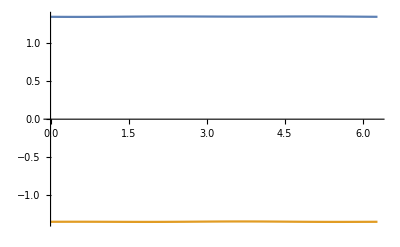

```mathematica
Plot[{δλ1[1,ϕ],δλ2[1,ϕ]},{ϕ,0,2π}] (*Eigenvalue vs angle of q*)
```

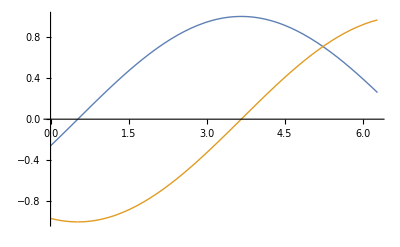
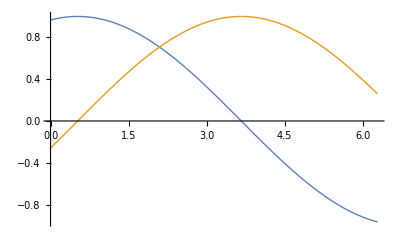

```mathematica
(*Eigenvectors components*)
{Plot[{Sign[ϕ-ϕk0]Normalize[V1[ϕ]]⟦1⟧,Sign[ϕ-ϕk0]Normalize[V1[ϕ]]⟦2⟧},{ϕ,0,2π},PlotStyle->{Thick,Thick,{LightBlue,Dashed},{LightOrange,Dashed}}],
Plot[{Sign[ϕ-ϕk0-π]Normalize[V2[ϕ]]⟦1⟧,Sign[ϕ-ϕk0-π]Normalize[V2[ϕ]]⟦2⟧},{ϕ,0,2π},PlotStyle->{Thick,Thick,{LightBlue,Dashed},{LightOrange,Dashed}}]}
```

#### Approx Eigenproblem

```mathematica
(*Here we aproximated the vector in M to the same magnitud in the four matrix entries, to obtain a approximated Cq that have the for as is defined en Capprox*)

(*With thes approximation we obtain the approximated eigenvalues and eigenvectors*)
m=Sum[Norm[M⟦i,j⟧],{i,2},{j,2}]/4 ;
Capprox[ϕ_]=m{{-Cos[(-ϕk0+ϕ)],-Sin[(-ϕk0+ϕ)]},{-Sin[(-ϕk0+ϕ)],Cos[(-ϕk0+ϕ)]}};
EigenTrig[ϕ_]=Eigensystem[Capprox[ϕ]];
δapprox1[qq_,ϕ_]=FullSimplify[qq EigenTrig[ϕ]⟦1,2⟧];
δapprox2[qq_,ϕ_]=FullSimplify[qq EigenTrig[ϕ]⟦1,1⟧];
f1approx[qq_,ϕ_]=Sqrt[(f0*2π)^2+δapprox1[qq,ϕ]]/(2π);
f2approx[qq_,ϕ_]=Sqrt[(f0*2π)^2+δapprox2[qq,ϕ]]/(2π);
Vapprox1[ϕ_]=FullSimplify[Chop[TrigFactor[EigenTrig[ϕ]⟦2,2⟧]]];
Vapprox2[ϕ_]=FullSimplify[Chop[TrigFactor[EigenTrig[ϕ]⟦2,1⟧]]];
Vnorm1[ϕ_]={Sin[(ϕ-ϕk0)/2],-Cos[(ϕ-ϕk0)/2]};
Vnorm2[ϕ_]={Cos[(ϕ-ϕk0)/2],Sin[(ϕ-ϕk0)/2]};
Print["The eigenproblem associted with the matrix", MatrixForm [q Capprox[ϕ]], " have theeigenvalues: ", δapprox1[q,ϕ],", ", δapprox2[q,ϕ], " and the eigenvectors ",MatrixForm@ Vnorm1[ϕ], ", ", MatrixForm@Vnorm2[ϕ]]
```

The eigenproblem associted with the matrix(-1.35339 q Cos[0.523599-ϕ] | 1.35339 q Sin[0.523599-ϕ]
1.35339 q Sin[0.523599-ϕ] | 1.35339 q Cos[0.523599-ϕ]) have theeigenvalues: 1.35339 q, -1.35339 q and the eigenvectors (Sin[1/2 (-0.523599+ϕ)]
-Cos[1/2 (-0.523599+ϕ)]), (Cos[1/2 (-0.523599+ϕ)]
Sin[1/2 (-0.523599+ϕ)])

```mathematica
f1apGrap=ParametricPlot3D[{kx+qq Cos[ϕ],ky+qq Sin[ϕ],f1approx[qq,ϕ]-Δf},{qq,0.00001,0.05Norm[k0]},{ϕ,0,2π},ColorFunction->"Aquamarine",PlotStyle->Directive[Opacity[0.7],Specularity[White,5]],Mesh->None];
f2apGrap=ParametricPlot3D[{kx+qq Cos[ϕ],ky+qq Sin[ϕ],f2approx[qq,ϕ]-Δf},{qq,0.00001,0.05Norm[k0]},{ϕ,0,2π},ColorFunction->"Aquamarine",PlotStyle->Directive[Opacity[0.7],Specularity[White,5]],Mesh->None];
Show[cone1GME,cone2GME,f1apGrap,f2apGrap,PlotRange->All]
```

-Graphics3D-

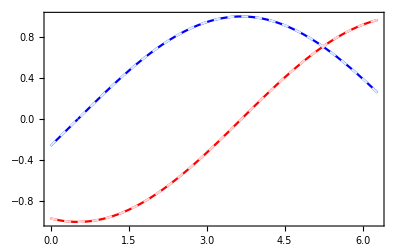

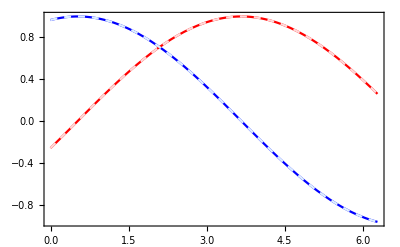

```mathematica
(*comparison between the exact analytical solution of the eigenproblem and the approximated solution based on the Capprox matrix*)
Plot[{-Sign [ϕk0-ϕ]Normalize[V1[ϕ]]⟦1⟧,-Sign [ϕk0-ϕ]Normalize[V1[ϕ]]⟦2⟧,Vnorm1[ϕ]⟦1⟧,Vnorm1[ϕ]⟦2⟧},{ϕ,0,2π},PlotStyle-> {Blue,Red,{LightBlue,Dashed},{LightRed,Dashed}},Frame->True]
Plot[{-Sign[ϕk0+π-ϕ]Normalize[V2[ϕ]]⟦1⟧,-Sign[ϕk0+π-ϕ]Normalize[V2[ϕ]]⟦2⟧,Vnorm2[ϕ]⟦1⟧,Vnorm2[ϕ]⟦2⟧},{ϕ,0,2π},PlotStyle-> {Blue,Red,{LightBlue,Dashed},{LightRed,Dashed}},Frame->True]
```

### Field Expansion

With the solution of the approximated matrix Capprox we found the k·p eigenvalues and the eigenvector of the k·p method and with thes evaluated the electric fields

#### Field Functions around K

```mathematica
Clear[Δk,R,Xx,Yy]
Δk[k_,ϕ_]:=k{Cos[ϕ],Sin[ϕ]};
k0={kx,ky}
Clear[x,y,z]
TK0i=AbsoluteTime[];
{K,frecsK,CoefMMK,HxxK,HyyK,HzzK,DxxK,DyyK,DzzK}=WVrec[k0,nb,1];
TK0f=AbsoluteTime[]-TK0i
```

{3.6276,2.0944}

10.511603

```mathematica
D0K=DxxK/.z->0 /.x->0 /.y->0;
θEK={ArcTan[Re[D0K⟦1⟧],Im[D0K⟦1⟧]],ArcTan[Re[D0K⟦2⟧],Im[D0K⟦2⟧]]};
CoefMMK=Chop[CoefMMK*Exp[-ⅈ θEK]];
{HzzK,DxxK,DyyK}={Chop[HzzK*Exp[-ⅈ θEK]],Chop[DxxK*Exp[-ⅈ θEK]],Chop[DyyK*Exp[-ⅈ θEK]]};
Clear[HxxK,HyyK,DzzK]
```

```mathematica
ϕK=ArcTan[K⟦1⟧,K⟦2⟧]
f0K=Mean[frecsK];
f1K[qq_]=Sqrt[(f0K*2π)^2+m qq]/(2π);
f2K[qq_]=Sqrt[(f0K*2π)^2-m qq]/(2π);
V1K[ϕ_]={Sin[(ϕ-ϕK)/2],-Cos[(ϕ-ϕK)/2]}
V2K[ϕ_]={Cos[(ϕ-ϕK)/2],Sin[(ϕ-ϕK)/2]}
Clear[E1x0K,E1y0K,E2x0K,E2y0K,E1xK,E1yK,E2xK,E2yK,Dx0K,Dy0K,Hz0K];
Dx0K[xp_,yp_]=(DxxK/.y->yp/.x->xp/.z->0);
Dy0K[xp_,yp_]=(DyyK/.y->yp/.x->xp/.z->0);
Hz0K[xp_,yp_]= HzzK/.y->yp/.x->xp/.z->0;
```

0.523599

{Sin[1/2 (-0.523599+ϕ)],-Cos[1/2 (-0.523599+ϕ)]}

{Cos[1/2 (-0.523599+ϕ)],Sin[1/2 (-0.523599+ϕ)]}

```mathematica
E1x0K[k_,ϕ_,x_,y_]:=E1x0K[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dx0K[x,y]⟦1⟧)(2π f0K)/Eps[x,y];
E2x0K[k_,ϕ_,x_,y_]:=E2x0K[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dx0K[x,y]⟦2⟧)(2π f0K)/Eps[x,y];
E1y0K[k_,ϕ_,x_,y_]:=E1y0K[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dy0K[x,y]⟦1⟧)(2π f0K)/Eps[x,y];
E2y0K[k_,ϕ_,x_,y_]:=E2y0K[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dy0K[x,y]⟦2⟧)(2π f0K)/Eps[x,y];

D1x0K[k_,ϕ_,x_,y_]:=D1x0K[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dx0K[x,y]⟦1⟧)(2π f0K);
D2x0K[k_,ϕ_,x_,y_]:=D2x0K[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dx0K[x,y]⟦2⟧)(2π f0K);
D1y0K[k_,ϕ_,x_,y_]:=D1y0K[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dy0K[x,y]⟦1⟧)(2π f0K);
D2y0K[k_,ϕ_,x_,y_]:=D2y0K[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dy0K[x,y]⟦2⟧)(2π f0K);

E1xK[k_,ϕ_,x_,y_]:=(V1K[ϕ]⟦1⟧(E1x0K[k,ϕ,x,y])+V1K[ϕ]⟦2⟧(E2x0K[k,ϕ,x,y]))/(2π f1K[k]);
E1yK[k_,ϕ_,x_,y_]:=(V1K[ϕ]⟦1⟧(E1y0K[k,ϕ,x,y])+V1K[ϕ]⟦2⟧(E2y0K[k,ϕ,x,y]))/(2π f1K[k]);
E2xK[k_,ϕ_,x_,y_]:=(V2K[ϕ]⟦1⟧(E1x0K[k,ϕ,x,y])+V2K[ϕ]⟦2⟧(E2x0K[k,ϕ,x,y]))/(2π f2K[k]);
E2yK[k_,ϕ_,x_,y_]:=(V2K[ϕ]⟦1⟧(E1y0K[k,ϕ,x,y])+V2K[ϕ]⟦2⟧(E2y0K[k,ϕ,x,y]))/(2π f2K[k]);

D1xK[k_,ϕ_,x_,y_]:=(V1K[ϕ]⟦1⟧(D1x0K[k,ϕ,x,y])+V1K[ϕ]⟦2⟧(D2x0K[k,ϕ,x,y]))/(2π f1K[k]);
D1yK[k_,ϕ_,x_,y_]:=(V1K[ϕ]⟦1⟧(D1y0K[k,ϕ,x,y])+V1K[ϕ]⟦2⟧(D2y0K[k,ϕ,x,y]))/(2π f1K[k]);
D2xK[k_,ϕ_,x_,y_]:=(V2K[ϕ]⟦1⟧(D1x0K[k,ϕ,x,y])+V2K[ϕ]⟦2⟧(D2x0K[k,ϕ,x,y]))/(2π f2K[k]);
D2yK[k_,ϕ_,x_,y_]:=(V2K[ϕ]⟦1⟧(D1y0K[k,ϕ,x,y])+V2K[ϕ]⟦2⟧(D2y0K[k,ϕ,x,y]))/(2π f2K[k]);
```

Comparison with Lukin
Here, we compare the fields of the k·p method with the ansatz proposed by Lukin at the center of the unit cell. It is made for the fields around tghe point K.

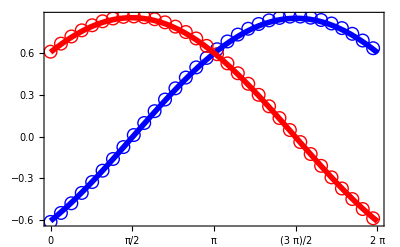

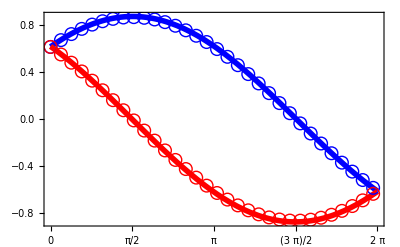

```mathematica
E1LukinK[ϕ_]:={Sqrt[0.75](Sin[ϕ/2-π/4]),Sqrt[0.75](Sin[ϕ/2+π/4])};
E2LukinK[ϕ_]:={Sqrt[0.75](Sin[ϕ/2+π/4]),-Sqrt[0.75](Sin[ϕ/2-π/4])};

GrapE1kp=Plot[{2^(1/4)Re[E1xK[0.03Norm[k0],ϕ,0,0]],2^(1/4)Re[E1yK[0.03Norm[k0],ϕ,0,0]]},{ϕ,0,2π},Frame->True,PlotStyle->{{Blue,Thickness[0.01]},{Red,Thickness[0.01]}}];
GrapE1Lukin=ListPlot[{Table[{ϕ,E1LukinK[ϕ]⟦1⟧},{ϕ,0,2π,0.2}],Table[{ϕ,E1LukinK[ϕ]⟦2⟧},{ϕ,0,2π,0.2}]},PlotStyle->{Blue,Red},PlotMarkers->{{"○",Medium}}];
Show[GrapE1Lukin,GrapE1kp,PlotRange->All,LabelStyle->Directive[Large,(FontFamily->"Times")],Frame-> True,FrameTicks->{{True,None},{{0,Pi/2,Pi,3Pi/2,2Pi},None}}]

GrapE2kp=Plot[{2^(1/4)Re[E2xK[0.03Norm[k0],ϕ,0,0]],2^(1/4)Re[E2yK[0.03Norm[k0],ϕ,0,0]]},{ϕ,0,2π},Frame->True,PlotStyle->{{Blue,Thickness[0.01]},{Red,Thickness[0.01]}}];
GrapE2Lukin=ListPlot[{Table[{ϕ,E2LukinK[ϕ]⟦1⟧},{ϕ,0,2π,0.2}],Table[{ϕ,E2LukinK[ϕ]⟦2⟧},{ϕ,0,2π,0.2}]},PlotStyle->{Blue,Red},PlotMarkers->{{"○",Medium}}];
Show[GrapE2kp,GrapE2Lukin,PlotRange->All,LabelStyle->Directive[Large,(FontFamily->"Times")],Frame-> True,FrameTicks->{{True,None},{{0,Pi/2,Pi,3Pi/2,2Pi},None}}]
```

#### Field Functions around Kp

```mathematica
Clear[Δk,R,Xx,Yy]
Δk[k_,ϕ_]:=k{Cos[ϕ],Sin[ϕ]};
k0={kx,-ky}
Clear[x,y,z]
TK0i=AbsoluteTime[];
{Kp,frecsKp,CoefMMKp,HxxKp,HyyKp,HzzKp,DxxKp,DyyKp,DzzKp}=WVrec[k0,nb,1];
TK0f=AbsoluteTime[]-TK0i
```

{3.6276,-2.0944}

10.506204

```mathematica
D0Kp=DxxKp/.z->0 /.x->0 /.y->0
θEKp={ArcTan[Re[D0Kp⟦1⟧],Im[D0Kp⟦1⟧]],ArcTan[Re[D0Kp⟦2⟧],Im[D0Kp⟦2⟧]]}
CoefMMKp=Chop[CoefMMKp*Exp[-ⅈ θEKp]];
{HzzKp,DxxKp,DyyKp}={Chop[HzzKp*Exp[-ⅈ θEKp]],Chop[DxxKp*Exp[-ⅈ θEKp]],Chop[DyyKp*Exp[-ⅈ θEKp]]};
Clear[HxxKp,HyyKp,DzzKp]
```

{0.-6.615 ⅈ,0.-3.85577 ⅈ}

{-1.5708,-1.5708}

```mathematica
ϕKp=ArcTan[Kp⟦1⟧,Kp⟦2⟧]
f0Kp=Mean[frecsKp];
f1Kp[qq_]=Sqrt[(f0Kp*2π)^2+m qq]/(2π);
f2Kp[qq_]=Sqrt[(f0Kp*2π)^2-m qq]/(2π);
V1Kp[ϕ_]={Sin[(ϕ-ϕKp)/2],Cos[(ϕ-ϕKp)/2]}
V2Kp[ϕ_]={-Cos[(ϕ-ϕKp)/2],Sin[(ϕ-ϕKp)/2]}
Clear[E1x0Kp,E1y0Kp,E2x0Kp,E2y0Kp,E1xKp,E1yKp,E2xKp,E2yKp,Dx0Kp,Dy0Kp,Hz0Kp];
Dx0Kp[xp_,yp_]=(DxxKp/.y->yp/.x->xp/.z->0);
Dy0Kp[xp_,yp_]=(DyyKp/.y->yp/.x->xp/.z->0);
Hz0Kp[xp_,yp_]= HzzKp/.y->yp/.x->xp/.z->0;
```

-0.523599

{Sin[1/2 (0.523599+ϕ)],Cos[1/2 (0.523599+ϕ)]}

{-Cos[1/2 (0.523599+ϕ)],Sin[1/2 (0.523599+ϕ)]}

```mathematica
E1x0Kp[k_,ϕ_,x_,y_]:=E1x0Kp[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dx0Kp[x,y]⟦1⟧)(2π f0Kp)/Eps[x,y];
E2x0Kp[k_,ϕ_,x_,y_]:=E2x0Kp[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dx0Kp[x,y]⟦2⟧)(2π f0Kp)/Eps[x,y];
E1y0Kp[k_,ϕ_,x_,y_]:=E1y0Kp[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dy0Kp[x,y]⟦1⟧)(2π f0Kp)/Eps[x,y];
E2y0Kp[k_,ϕ_,x_,y_]:=E2y0Kp[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dy0Kp[x,y]⟦2⟧)(2π f0Kp)/Eps[x,y];

D1x0Kp[k_,ϕ_,x_,y_]:=D1x0Kp[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dx0Kp[x,y]⟦1⟧)(2π f0Kp);
D2x0Kp[k_,ϕ_,x_,y_]:=D2x0Kp[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dx0Kp[x,y]⟦2⟧)(2π f0Kp);
D1y0Kp[k_,ϕ_,x_,y_]:=D1y0Kp[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dy0Kp[x,y]⟦1⟧)(2π f0Kp);
D2y0Kp[k_,ϕ_,x_,y_]:=D2y0Kp[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dy0Kp[x,y]⟦2⟧)(2π f0Kp);

E1xKp[k_,ϕ_,x_,y_]:=(V1Kp[ϕ]⟦1⟧(E1x0Kp[k,ϕ,x,y])+V1Kp[ϕ]⟦2⟧(E2x0Kp[k,ϕ,x,y]))/(2π f1Kp[k]);
E1yKp[k_,ϕ_,x_,y_]:=(V1Kp[ϕ]⟦1⟧(E1y0Kp[k,ϕ,x,y])+V1Kp[ϕ]⟦2⟧(E2y0Kp[k,ϕ,x,y]))/(2π f1Kp[k]);
E2xKp[k_,ϕ_,x_,y_]:=(V2Kp[ϕ]⟦1⟧(E1x0Kp[k,ϕ,x,y])+V2Kp[ϕ]⟦2⟧(E2x0Kp[k,ϕ,x,y]))/(2π f2Kp[k]);
E2yKp[k_,ϕ_,x_,y_]:=(V2Kp[ϕ]⟦1⟧(E1y0Kp[k,ϕ,x,y])+V2Kp[ϕ]⟦2⟧(E2y0Kp[k,ϕ,x,y]))/(2π f2Kp[k]);

D1xKp[k_,ϕ_,x_,y_]:=(V1Kp[ϕ]⟦1⟧(D1x0Kp[k,ϕ,x,y])+V1Kp[ϕ]⟦2⟧(D2x0Kp[k,ϕ,x,y]))/(2π f1Kp[k]);
D1yKp[k_,ϕ_,x_,y_]:=(V1Kp[ϕ]⟦1⟧(D1y0Kp[k,ϕ,x,y])+V1Kp[ϕ]⟦2⟧(D2y0Kp[k,ϕ,x,y]))/(2π f1Kp[k]);
D2xKp[k_,ϕ_,x_,y_]:=(V2Kp[ϕ]⟦1⟧(D1x0Kp[k,ϕ,x,y])+V2Kp[ϕ]⟦2⟧(D2x0Kp[k,ϕ,x,y]))/(2π f2Kp[k]);
D2yKp[k_,ϕ_,x_,y_]:=(V2Kp[ϕ]⟦1⟧(D1y0Kp[k,ϕ,x,y])+V2Kp[ϕ]⟦2⟧(D2y0Kp[k,ϕ,x,y]))/(2π f2Kp[k]);
```

Comparison with Lukin
Here, we compare the fields of the k·p method with the ansatz proposed by Lukin at the center of the unit cell. It is made for the fields around tghe point K’.

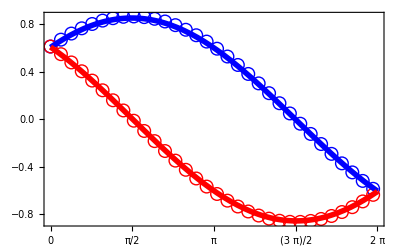

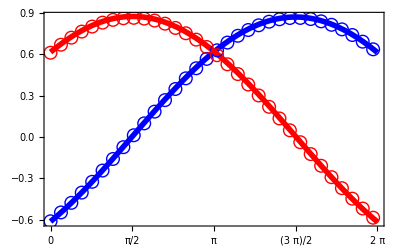

```mathematica
E1LukinKp[ϕ_]:={Sqrt[0.75](Sin[ϕ/2+π/4]),-Sqrt[0.75](Sin[ϕ/2-π/4])};
E2LukinKp[ϕ_]:={Sqrt[0.75](Sin[ϕ/2-π/4]),Sqrt[0.75](Sin[ϕ/2+π/4])};

GrapE1kp=Plot[{2^(1/4)Re[E1xKp[0.03Norm[k0],ϕ,0,0]],2^(1/4)Re[E1yKp[0.03Norm[k0],ϕ,0,0]]},{ϕ,0,2π},Frame->True,PlotStyle->{{Blue,Thickness[0.01]},{Red,Thickness[0.01]}}];
GrapE1Lukin=ListPlot[{Table[{ϕ,E1LukinKp[ϕ]⟦1⟧},{ϕ,0,2π,0.2}],Table[{ϕ,E1LukinKp[ϕ]⟦2⟧},{ϕ,0,2π,0.2}]},PlotStyle->{Blue,Red},PlotMarkers->{{"○",Medium}}];
Show[GrapE1Lukin,GrapE1kp,PlotRange->All,LabelStyle->Directive[Large,(FontFamily->"Times")],Frame-> True,FrameTicks->{{True,None},{{0,Pi/2,Pi,3Pi/2,2Pi},None}}]

GrapE2kp=Plot[{2^(1/4)Re[E2xKp[0.03Norm[k0],ϕ,0,0]],2^(1/4)Re[E2yKp[0.03Norm[k0],ϕ,0,0]]},{ϕ,0,2π},Frame->True,PlotStyle->{{Blue,Thickness[0.01]},{Red,Thickness[0.01]}}];
GrapE2Lukin=ListPlot[{Table[{ϕ,E2LukinKp[ϕ]⟦1⟧},{ϕ,0,2π,0.2}],Table[{ϕ,E2LukinKp[ϕ]⟦2⟧},{ϕ,0,2π,0.2}]},PlotStyle->{Blue,Red},PlotMarkers->{{"○",Medium}}];
Show[GrapE2kp,GrapE2Lukin,PlotRange->All,LabelStyle->Directive[Large,(FontFamily->"Times")],Frame-> True,FrameTicks->{{True,None},{{0,Pi/2,Pi,3Pi/2,2Pi},None}}]
```

#### Field In The Unit Cell for k around K

Here, the notebook calculate the fields for a k around K using the k·p method, they can be evaluated in the whole unit cell.

```mathematica
k1
Nq=Norm[k1-K]
Nq/Norm[K]
ϕq=ArcTan[(k1-K)⟦1⟧,(k1-K)⟦2⟧]
```

{3.75326,2.0944}

0.125664

0.03

0.

```mathematica
E1xKlist=ParallelTable[{RHex⟦i,1⟧,RHex⟦i,2⟧, E1xK[Nq,ϕq,RHex⟦i,1⟧,RHex⟦i,2⟧]},{i,Length[RHex]}];
E1yKlist=ParallelTable[{RHex⟦i,1⟧,RHex⟦i,2⟧, E1yK[Nq,ϕq,RHex⟦i,1⟧,RHex⟦i,2⟧]},{i,Length[RHex]}];
E2xKlist=ParallelTable[{RHex⟦i,1⟧,RHex⟦i,2⟧, E2xK[Nq,ϕq,RHex⟦i,1⟧,RHex⟦i,2⟧]},{i,Length[RHex]}];
E2yKlist=ParallelTable[{RHex⟦i,1⟧,RHex⟦i,2⟧, E2yK[Nq,ϕq,RHex⟦i,1⟧,RHex⟦i,2⟧]},{i,Length[RHex]}];
```

```mathematica
ReE1xKlist=Table[{Elist⟦1⟧,Elist⟦2⟧,Re[Elist⟦3⟧]},{Elist,E1xKlist}];
ReE1yKlist=Table[{Elist⟦1⟧,Elist⟦2⟧,Re[Elist⟦3⟧]},{Elist,E1yKlist}];
ImE1xKlist=Table[{Elist⟦1⟧,Elist⟦2⟧,Im[Elist⟦3⟧]},{Elist,E1xKlist}];
ImE1yKlist=Table[{Elist⟦1⟧,Elist⟦2⟧,Im[Elist⟦3⟧]},{Elist,E1yKlist}];
SqE1Klist=Table[{E1xKlist⟦i,1⟧,E1xKlist⟦i,2⟧,Sqrt[Abs[E1xKlist⟦i,3⟧]^2+Abs[E1yKlist⟦i,3⟧]^2]},{i,Length[E1xKlist]}];

ReE2xKlist=Table[{Elist⟦1⟧,Elist⟦2⟧,Re[Elist⟦3⟧]},{Elist,E2xKlist}];
ReE2yKlist=Table[{Elist⟦1⟧,Elist⟦2⟧,Re[Elist⟦3⟧]},{Elist,E2yKlist}];
ImE2xKlist=Table[{Elist⟦1⟧,Elist⟦2⟧,Im[Elist⟦3⟧]},{Elist,E2xKlist}];
ImE2yKlist=Table[{Elist⟦1⟧,Elist⟦2⟧,Im[Elist⟦3⟧]},{Elist,E2yKlist}];
SqE2Klist=Table[{E2xKlist⟦i,1⟧,E2xKlist⟦i,2⟧,Sqrt[Abs[E2xKlist⟦i,3⟧]^2+Abs[E2yKlist⟦i,3⟧]^2]},{i,Length[E2xKlist]}];
```

```mathematica
MinSqEKkp=Min[Join[SqE1Klist⟦All,3⟧,SqE2Klist⟦All,3⟧]];
MaxSqEKkp=Max[Join[SqE1Klist⟦All,3⟧,SqE2Klist⟦All,3⟧]];
```

```mathematica
GraphE1Kkp=ListDensityPlot[SqE1Klist,PlotRange->All,ColorFunctionScaling->False,ColorFunction->(Blend[{{MinSqEKkp,White},{(MinSqEKkp+MaxSqEKkp)0.3,Yellow},{0.6MaxSqEKkp,Red},{MaxSqEKkp,Darker[Red]}},#]&),AspectRatio->Automatic,PlotLegends->Placed[Automatic,Right],LabelStyle->Directive[Bold, Medium],Frame-> {{True,None},{True,None}},FrameTicksStyle->{{Black,Thick}},AxesStyle->Directive[Black,Thick]]
GraphE2Kkp=ListDensityPlot[SqE2Klist,PlotRange->All,ColorFunctionScaling->False,ColorFunction->(Blend[{{MinSqEKkp,White},{(MinSqEKkp+MaxSqEKkp)0.3,Yellow},{0.6MaxSqEKkp,Red},{MaxSqEKkp,Darker[Red]}},#]&),AspectRatio->Automatic,PlotLegends->Placed[Automatic,Right],LabelStyle->Directive[Bold, Medium],Frame-> {{True,None},{True,None}},FrameTicksStyle->{{Black,Thick}},AxesStyle->Thick]
```

-Graphics-

-Graphics-

#### GME Fields for k around K

Here, the notebook evaluate the fields in the unit cell using the GME method, to campare the results with the k·p aprooximation. We use a k1 whose GME-matrix elements was evaluated previously on the notebook 1-GME.nb.

```mathematica
k1
Nq=Norm[k1-K]
Nq/Norm[K]
ϕq=ArcTan[(k1-K)⟦1⟧,(k1-K)⟦2⟧]
```

{3.75326,2.0944}

0.125664

0.03

0.

```mathematica
T0k=AbsoluteTime[];
eigenk=WVreck[1,nb,1];
res0={};
Do[AppendTo[res0,{Norm[k1],eigenk⟦2,i⟧}],{i,nb}];
Tk=AbsoluteTime[]-T0k
```

10.481686

```mathematica
Clear[Dx1GMEk,Dy1GMEk,Dx2GMEk,Dy2GMEk]
Dx1GMEk[xp_,yp_]=eigenk⟦7,1⟧/.x->xp/.y->yp/.z->0;
Dy1GMEk[xp_,yp_]=eigenk⟦8,1⟧/.x->xp/.y->yp/.z->0;

Dx2GMEk[xp_,yp_]=eigenk⟦7,2⟧/.x->xp/.y->yp/.z->0;
Dy2GMEk[xp_,yp_]=eigenk⟦8,2⟧/.x->xp/.y->yp/.z->0;
```

```mathematica
Ex1GMEk[xp_,yp_]:=Dx1GMEk[xp,yp]/Eps[xp,yp];
Ex2GMEk[xp_,yp_]:=Dx2GMEk[xp,yp]/Eps[xp,yp];
Δθ1=ArcTan[Re[Ex1GMEk[0,0]/E1xK[Nq,ϕq,0,0]],Im[Ex1GMEk[0,0]/E1xK[Nq,ϕq,0,0]]];
Δθ2=ArcTan[Re[Ex2GMEk[0,0]/E2xK[Nq,ϕq,0,0]],Im[Ex2GMEk[0,0]/E2xK[Nq,ϕq,0,0]]];
Ex1GMEk[xp_,yp_]:=Chop[Exp[-ⅈ Δθ1]Dx1GMEk[xp,yp]/Eps[xp,yp]];
Ey1GMEk[xp_,yp_]:=Chop[Exp[-ⅈ Δθ1]Dy1GMEk[xp,yp]/Eps[xp,yp]];
Ex2GMEk[xp_,yp_]:=Chop[Exp[-ⅈ Δθ2]Dx2GMEk[xp,yp]/Eps[xp,yp]];
Ey2GMEk[xp_,yp_]:=Chop[Exp[-ⅈ Δθ2]Dy2GMEk[xp,yp]/Eps[xp,yp]];
```

```mathematica
SqE1KlistGME=ParallelTable[{r⟦1⟧,r⟦2⟧,Sqrt[Abs[Ex1GMEk[r⟦1⟧,r⟦2⟧]]^2+Abs[Ey1GMEk[r⟦1⟧,r⟦2⟧]]^2]},{r,RHex}];
SqE2KlistGME=ParallelTable[{r⟦1⟧,r⟦2⟧,Sqrt[Abs[Ex2GMEk[r⟦1⟧,r⟦2⟧]]^2+Abs[Ey2GMEk[r⟦1⟧,r⟦2⟧]]^2]},{r,RHex}];

MinSqEKGME=Min[Join[SqE1KlistGME⟦All,3⟧,SqE2KlistGME⟦All,3⟧]];
MaxSqEKGME=Max[Join[SqE1KlistGME⟦All,3⟧,SqE2KlistGME⟦All,3⟧]];
```

```mathematica
GraphE1KGME=ListDensityPlot[SqE1KlistGME,PlotRange->All,ColorFunctionScaling->False,ColorFunction->(Blend[{{MinSqEKGME,White},{(MinSqEKGME+MaxSqEKGME)0.3,Yellow},{0.6MaxSqEKGME,Red},{MaxSqEKGME,Darker[Red]}},#]&),AspectRatio->Automatic,PlotLegends->Placed[Automatic,Right],LabelStyle->Directive[Bold, Medium],Frame-> {{True,None},{True,None}},FrameTicksStyle->{{Black,Thick}},AxesStyle->Thick]
GraphE2KGME=ListDensityPlot[SqE2KlistGME,PlotRange->All,ColorFunctionScaling->False,ColorFunction->(Blend[{{MinSqEKGME,White},{(MinSqEKGME+MaxSqEKGME)0.3,Yellow},{0.6MaxSqEKGME,Red},{MaxSqEKGME,Darker[Red]}},#]&),AspectRatio->Automatic,PlotLegends->Placed[Automatic,Right],LabelStyle->Directive[Bold, Medium],Frame-> {{True,None},{True,None}},FrameTicksStyle->{{Black,Thick}},AxesStyle->Thick]
```

-Graphics-

-Graphics-

#### Comparison GME-kP for k around K

Here, we compare the results of the GME and the k·p approximation. We quantify the differences by taking the square difference between the electric field of each method evaluated different positions in a mesh into the unit cell, and finally summing the difference in all the positions. To construct a relative measure, we divide this sum by the mean square value.

```mathematica
SqΔE1k=ParallelTable[{r⟦1⟧,r⟦2⟧,Abs[Ex1GMEk[r⟦1⟧,r⟦2⟧]-E1xK[Nq,ϕq,r⟦1⟧,r⟦2⟧]]^2+Abs[Ey1GMEk[r⟦1⟧,r⟦2⟧]-E1yK[Nq,ϕq,r⟦1⟧,r⟦2⟧]]^2},{r,RHex}];
σ1k=Sum[SqΔE1k⟦i,3⟧,{i,Length[SqΔE1k]}]/Length[SqΔE1k];
SqE1kmean=Sum[SqE1Klist⟦i,3⟧^2,{i,Length[SqE1Klist]}]/Length[SqE1Klist];

SqΔE2k=ParallelTable[{r⟦1⟧,r⟦2⟧,Abs[Ex2GMEk[r⟦1⟧,r⟦2⟧]-E2xK[Nq,ϕq,r⟦1⟧,r⟦2⟧]]^2+Abs[Ey2GMEk[r⟦1⟧,r⟦2⟧]-E2yK[Nq,ϕq,r⟦1⟧,r⟦2⟧]]^2},{r,RHex}];
σ2k=Sum[SqΔE2k⟦i,3⟧,{i,Length[SqΔE2k]}]/Length[SqΔE2k];
SqE2kmean=Sum[SqE2Klist⟦i,3⟧^2,{i,Length[SqE2Klist]}]/Length[SqE2Klist];
```

```mathematica
(*Relative quantification of the deviation between GME and k·p, for the electric field of the upper and lower bands*)
Sqrt[σ1k/SqE1kmean]
Sqrt[σ2k/SqE2kmean]
```

0.0697003

0.0638326

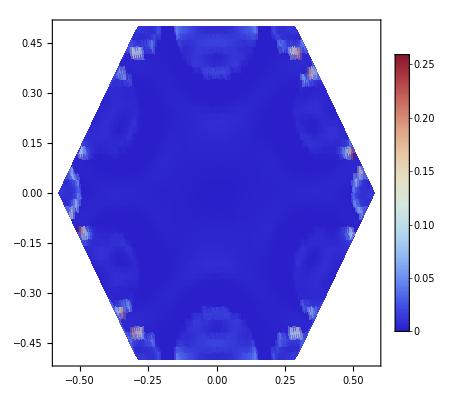

```mathematica
ListDensityPlot[SqΔE1k,ColorFunction->"ThermometerColors",PlotRange->All,PlotLegends->Automatic]
```

#### Field In The Unit Cell for k around Kp

Here, the notebook calculate the fields for a k around K’ using the k·p method, they can be evaluated in the whole unit cell.

```mathematica
kp1
Nq=Norm[kp1-Kp]
Nq/Norm[Kp]
ϕq=ArcTan[(kp1-Kp)⟦1⟧,(kp1-Kp)⟦2⟧]
```

{3.75326,-2.0944}

0.125664

0.03

0.

```mathematica
E1xKplist=ParallelTable[{RHex⟦i,1⟧,RHex⟦i,2⟧, E1xKp[Nq,ϕq,RHex⟦i,1⟧,RHex⟦i,2⟧]},{i,Length[RHex]}];
E1yKplist=ParallelTable[{RHex⟦i,1⟧,RHex⟦i,2⟧, E1yKp[Nq,ϕq,RHex⟦i,1⟧,RHex⟦i,2⟧]},{i,Length[RHex]}];
E2xKplist=ParallelTable[{RHex⟦i,1⟧,RHex⟦i,2⟧, E2xKp[Nq,ϕq,RHex⟦i,1⟧,RHex⟦i,2⟧]},{i,Length[RHex]}];
E2yKplist=ParallelTable[{RHex⟦i,1⟧,RHex⟦i,2⟧, E2yKp[Nq,ϕq,RHex⟦i,1⟧,RHex⟦i,2⟧]},{i,Length[RHex]}];
```

```mathematica
ReE1xKplist=Table[{Elist⟦1⟧,Elist⟦2⟧,Re[Elist⟦3⟧]},{Elist,E1xKplist}];
ReE1yKplist=Table[{Elist⟦1⟧,Elist⟦2⟧,Re[Elist⟦3⟧]},{Elist,E1yKplist}];
ImE1xKplist=Table[{Elist⟦1⟧,Elist⟦2⟧,Im[Elist⟦3⟧]},{Elist,E1xKplist}];
ImE1yKplist=Table[{Elist⟦1⟧,Elist⟦2⟧,Im[Elist⟦3⟧]},{Elist,E1yKplist}];
SqE1Kplist=Table[{E1xKplist⟦i,1⟧,E1xKplist⟦i,2⟧,Sqrt[Abs[E1xKplist⟦i,3⟧]^2+Abs[E1yKplist⟦i,3⟧]^2]},{i,Length[E1xKplist]}];

ReE2xKplist=Table[{Elist⟦1⟧,Elist⟦2⟧,Re[Elist⟦3⟧]},{Elist,E2xKplist}];
ReE2yKplist=Table[{Elist⟦1⟧,Elist⟦2⟧,Re[Elist⟦3⟧]},{Elist,E2yKplist}];
ImE2xKplist=Table[{Elist⟦1⟧,Elist⟦2⟧,Im[Elist⟦3⟧]},{Elist,E2xKplist}];
ImE2yKplist=Table[{Elist⟦1⟧,Elist⟦2⟧,Im[Elist⟦3⟧]},{Elist,E2yKplist}];
SqE2Kplist=Table[{E2xKplist⟦i,1⟧,E2xKplist⟦i,2⟧,Sqrt[Abs[E2xKplist⟦i,3⟧]^2+Abs[E2yKplist⟦i,3⟧]^2]},{i,Length[E2xKplist]}];
```

```mathematica
MinSqEKpkp=Min[Join[SqE1Kplist⟦All,3⟧,SqE2Kplist⟦All,3⟧]];
MaxSqEKpkp=Max[Join[SqE1Kplist⟦All,3⟧,SqE2Kplist⟦All,3⟧]];
```

```mathematica
GraphE1Kpkp=ListDensityPlot[SqE1Kplist,PlotRange->All,ColorFunctionScaling->False,ColorFunction->(Blend[{{MinSqEKpkp,White},{(MinSqEKpkp+MaxSqEKpkp)0.3,Yellow},{0.6MaxSqEKpkp,Red},{MaxSqEKpkp,Darker[Red]}},#]&),AspectRatio->Automatic,PlotLegends->Placed[Automatic,Right],LabelStyle->Directive[Bold, Medium],Frame-> {{True,None},{True,None}},FrameTicksStyle->{{Black,Thick}},AxesStyle->Directive[Black,Thick]]
GraphE2Kpkp=ListDensityPlot[SqE2Kplist,PlotRange->All,ColorFunctionScaling->False,ColorFunction->(Blend[{{MinSqEKpkp,White},{(MinSqEKpkp+MaxSqEKpkp)0.3,Yellow},{0.6MaxSqEKpkp,Red},{MaxSqEKpkp,Darker[Red]}},#]&),AspectRatio->Automatic,PlotLegends->Placed[Automatic,Right],LabelStyle->Directive[Bold, Medium],Frame-> {{True,None},{True,None}},FrameTicksStyle->{{Black,Thick}},AxesStyle->Thick]
Export["ArticleProposal/Supporting Info/GME Comparison/Upper-Band-k1p-kp.pdf",GraphE1Kpkp]
Export["ArticleProposal/Supporting Info/GME Comparison/Lower-Band-k1p-kp.pdf",GraphE2Kpkp]
```

-Graphics-

-Graphics-

ArticleProposal/Supporting Info/GME Comparison/Upper-Band-k1p-kp.pdf

ArticleProposal/Supporting Info/GME Comparison/Lower-Band-k1p-kp.pdf

#### GME Fields for k around Kp

Here, the notebook evaluate the fields in the unit cell using the GME method, to campare the results with the k·p aprooximation. We use a k1 whose GME-matrix elements was evaluated previously on the notebook 1-GME.nb.

```mathematica
T0k=AbsoluteTime[];
eigenkp=WVrecEquikp[1,nb,1];
res0={};
Do[AppendTo[res0,{Norm[kp1],eigenkp⟦2,i⟧}],{i,nb}];
Tk=AbsoluteTime[]-T0k
```

8.790913

```mathematica
Clear[Dx1GMEkp,Dy1GMEkp,Dx2GMEkp,Dy2GMEkp]
Dx1GMEkp[xp_,yp_]=eigenkp⟦7,1⟧/.x->xp/.y->yp/.z->0;
Dy1GMEkp[xp_,yp_]=eigenkp⟦8,1⟧/.x->xp/.y->yp/.z->0;

Dx2GMEkp[xp_,yp_]=eigenkp⟦7,2⟧/.x->xp/.y->yp/.z->0;
Dy2GMEkp[xp_,yp_]=eigenkp⟦8,2⟧/.x->xp/.y->yp/.z->0;
```

```mathematica
Ex1GMEkp[xp_,yp_]:=Dx1GMEkp[xp,yp]/Eps[xp,yp];
Ex2GMEkp[xp_,yp_]:=Dx2GMEkp[xp,yp]/Eps[xp,yp];
Δθ1=ArcTan[Re[Ex1GMEkp[0,0]/E1xKp[Nq,ϕq,0,0]],Im[Ex1GMEkp[0,0]/E1xKp[Nq,ϕq,0,0]]];
Δθ2=ArcTan[Re[Ex2GMEkp[0,0]/E2xKp[Nq,ϕq,0,0]],Im[Ex2GMEkp[0,0]/E2xKp[Nq,ϕq,0,0]]];
Ex1GMEkp[xp_,yp_]:=Chop[Exp[-ⅈ Δθ1]Dx1GMEkp[xp,yp]/Eps[xp,yp]];
Ey1GMEkp[xp_,yp_]:=Chop[Exp[-ⅈ Δθ1]Dy1GMEkp[xp,yp]/Eps[xp,yp]];
Ex2GMEkp[xp_,yp_]:=Chop[Exp[-ⅈ Δθ2]Dx2GMEkp[xp,yp]/Eps[xp,yp]];
Ey2GMEkp[xp_,yp_]:=Chop[Exp[-ⅈ Δθ2]Dy2GMEkp[xp,yp]/Eps[xp,yp]];
```

```mathematica
Ex2GMEkp[0,0]
Chop[E2xKp[Nq,ϕq,0,0]]
```

-0.50456

-0.516204

```mathematica
SqE1KplistGME=ParallelTable[{r⟦1⟧,r⟦2⟧,Sqrt[Abs[Ex1GMEkp[r⟦1⟧,r⟦2⟧]]^2+Abs[Ey1GMEkp[r⟦1⟧,r⟦2⟧]]^2]},{r,RHex}];
SqE2KplistGME=ParallelTable[{r⟦1⟧,r⟦2⟧,Sqrt[Abs[Ex2GMEkp[r⟦1⟧,r⟦2⟧]]^2+Abs[Ey2GMEkp[r⟦1⟧,r⟦2⟧]]^2]},{r,RHex}];

MinSqEKpGME=Min[Join[SqE1KplistGME⟦All,3⟧,SqE2KplistGME⟦All,3⟧]];
MaxSqEKpGME=Max[Join[SqE1KplistGME⟦All,3⟧,SqE2KplistGME⟦All,3⟧]];
```

```mathematica
GraphE1KpGME=ListDensityPlot[SqE1KplistGME,PlotRange->All,ColorFunctionScaling->False,ColorFunction->(Blend[{{MinSqEKpGME,White},{(MinSqEKpGME+MaxSqEKpGME)0.3,Yellow},{0.6MaxSqEKpGME,Red},{MaxSqEKpGME,Darker[Red]}},#]&),AspectRatio->Automatic,PlotLegends->Placed[Automatic,Right],LabelStyle->Directive[Bold, Medium],Frame-> {{True,None},{True,None}},FrameTicksStyle->{{Black,Thick}},AxesStyle->Thick]
GraphE2KpGME=ListDensityPlot[SqE2KplistGME,PlotRange->All,ColorFunctionScaling->False,ColorFunction->(Blend[{{MinSqEKpGME,White},{(MinSqEKpGME+MaxSqEKpGME)0.3,Yellow},{0.6MaxSqEKpGME,Red},{MaxSqEKpGME,Darker[Red]}},#]&),AspectRatio->Automatic,PlotLegends->Placed[Automatic,Right],LabelStyle->Directive[Bold, Medium],Frame-> {{True,None},{True,None}},FrameTicksStyle->{{Black,Thick}},AxesStyle->Thick]
Export["ArticleProposal/Supporting Info/GME Comparison/Upper-Band-k1p-GME.pdf",GraphE1KpGME]
Export["ArticleProposal/Supporting Info/GME Comparison/Lower-Band-k1p-GME.pdf",GraphE2KpGME]
```

-Graphics-

-Graphics-

ArticleProposal/Supporting Info/GME Comparison/Upper-Band-k1p-GME.pdf

ArticleProposal/Supporting Info/GME Comparison/Lower-Band-k1p-GME.pdf

#### Comparison GME-kP for k around Kp

Here, we compare the results of the GME and the k·p approximation. We quantify the differences by taking the square difference between the electric field of each method evaluated different positions in a mesh into the unit cell, and finally summing the difference in all the positions. To construct a relative measure, we divide this sum by the mean square value.

```mathematica
SqΔE1kp=Table[{r⟦1⟧,r⟦2⟧,Abs[Ex1GMEkp[r⟦1⟧,r⟦2⟧]-E1xKp[Nq,ϕq,r⟦1⟧,r⟦2⟧]]^2+Abs[Ey1GMEkp[r⟦1⟧,r⟦2⟧]-E1yKp[Nq,ϕq,r⟦1⟧,r⟦2⟧]]^2},{r,RHex}];
σ1kp=Sum[SqΔE1kp⟦i,3⟧,{i,Length[SqΔE1kp]}]/Length[SqΔE1kp];
SqE1kpmean=Sum[SqE1Kplist⟦i,3⟧^2,{i,Length[SqE1Kplist]}]/Length[SqE1Kplist];

SqΔE2kp=Table[{r⟦1⟧,r⟦2⟧,Abs[Ex2GMEkp[r⟦1⟧,r⟦2⟧]-E2xKp[Nq,ϕq,r⟦1⟧,r⟦2⟧]]^2+Abs[Ey2GMEkp[r⟦1⟧,r⟦2⟧]-E2yKp[Nq,ϕq,r⟦1⟧,r⟦2⟧]]^2},{r,RHex}];
σ2kp=Sum[SqΔE2kp⟦i,3⟧,{i,Length[SqΔE2kp]}]/Length[SqΔE2kp];
SqE2kpmean=Sum[SqE2Kplist⟦i,3⟧^2,{i,Length[SqE2Kplist]}]/Length[SqE2Kplist];
```

```mathematica
Sqrt[σ1kp/SqE1kpmean]
Sqrt[σ2kp/SqE2kpmean]
```

0.0697003

0.0638326

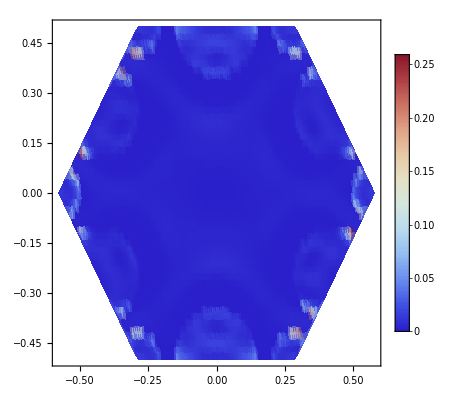

```mathematica
ListDensityPlot[SqΔE1kp,ColorFunction->"ThermometerColors",PlotRange->All,PlotLegends->Automatic]
```